◼ "\◼ "2023-11-25v2 .00M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Thermal quantum field theory

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Auxiliary material and code for App. C. “Thermal quantum field theory” of  [M. J. Steil, - 2023 - PhD thesis]

Includes codepackages nb, nf, Actor, and GL.
Note that grey cells and sections are NonEvaluating (Evaluatable->False) and to enable the involved computations their cell style needs to be changed back to their standard variants, e.g., NonEvaluatingInput → Input.

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

#### Methods — IO only

(** Update tagged methods **)
Needs["UpdateTaggedMethod`","D:/Github/Mathematica/Packages/UpdateTaggedMethod/UpdateTaggedMethod.m"];
UpdateTaggedMethods["D:/Github/Mathematica/tagged_methods.nb"]

```mathematica
(* AutoCollapse | v2.0 | Close CellGroup | [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(* CellPrintDisplayFormulaNumbered | v2.0 | CellPrint a DisplayFormulaNumbered *)
ClearAll[CellPrintDisplayFormulaNumbered];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:=Module[{frameLabels,box},
	frameLabels=CellFrameLabels->{{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},{None,None}};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,
		GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";
```

```mathematica
(* SaveToCell | v2.0 | Save assigned value of symbol(s) to cell(s) | Modified Version of [http://szhorvat.net/pelican/save-data-in-notebooks.html] *)
ClearAll[SaveToCell];
SaveToCell[names_/;VectorQ[names,StringQ],suffix:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=Module[{
	data=Symbol[#]&/@names,
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@MapThread[RowBox[{#2<>suffix,"=",ToBoxes[Iconize[#1,label,Method->Compress]],";"}]&,{data,names}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[{
	data=Evaluate[var],
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@RowBox[{If[name=!="",name,MakeBoxes[var]],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]
SaveToCell::usage="SaveToCell[var_,name:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignment of var/or the data in\
 var (under name if name=!=\"\") in a compressed iconized form with a label including comment and a time stamp.\n\
SaveToCell[names_/;VectorQ[names,StringQ],suffix_:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignments behind the elements of names in\
 in a compressed iconized form with suffix appended to the symbol names and a label including comment and a time stamp.";
```

## C.1. Grand canonical partition function

Computations for the App. C.1. “Grand canonical partition function” [M. J. Steil, - 2023 - PhD thesis]

```mathematica
Ω[T,μ]==-1/(β V)Log[Z[T,μ]];
Zrule=First@Solve[%,Z[T,μ],Assumptions->{Ω[T,μ]∈Reals,β∈Reals,V∈Reals}]/.β->1/T;
Row[{%[[1,1]],"=",%[[1,2]]}]//CellPrintDisplayFormulaNumbered
```

Z[T,μ]"="ⅇ^(-(V Ω[T,μ])/T)

```mathematica
{
	f->-T/V Log[Z[T,μ]],
	p->Inactive[D][T Log[Z[T,μ]],V],
	s->1/V Inactive[D][T Log[Z[T,μ]],T],
	n->1/V Inactive[D][T Log[Z[T,μ]],μ]
};
Row[{#[[1]],"=",#[[2]],"=",(#[[2]]/.Zrule/.Log[Exp[x___]]:>x//Activate)}]&/@%//TableForm//CellPrintDisplayFormulaNumbered
```

f"="-(T Log[Z[T,μ]])/V"="Ω[T,μ]
p"="Inactive(T Log[Z[T,μ]])V"="-Ω[T,μ]
s"="(Inactive(T Log[Z[T,μ]])T)/V"="-Ω^(1,0)[T,μ]
n"="(Inactive(T Log[Z[T,μ]])μ)/V"="-Ω^(0,1)[T,μ]

## C.2. Selected Matsubara sums and identities for distribution functions

Computations for the App. C.2. “Selected Matsubara sums and identities for distribution functions” [M. J. Steil, - 2023 - PhD thesis] and nb and nf codepackage(s)

## Distribution functions nb and nf

ClearAll["nb","nb`*"]
nb`ωn[n_,β_:β]:=(2π)/β(n)

nb`expRule=nb[x_]:>1/(Exp[x]-1);
nb`expRuleInv=Exp[x_]:>(1+nb[x])/nb[x];
nb`trigRule=nb[x_]:>1/2(Coth[x/2]-1);
nb`trigRuleInv=Coth[x_]:>1+2nb[2x];

nb[x]/.nb`expRule/.nb`expRuleInv//Simplify;
nb[x]/.nb`trigRule/.nb`trigRuleInv//Simplify;

nblist={{nb[x],(nb[x]/.nb`trigRule),nb[x]}};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],Simplify@TrigToExp[d[[2]]]/.nb`expRuleInv//Simplify}]};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nblist[[;;,1]],nblist[[;;,3]]}]]}]};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nblist[[;;,1]],nblist[[;;,3]]}]]}]};
nb`derivativeRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nblist[[2;;]][[All,{1,3}]]//Activate;
nb`derivativeTrigRules={nb`trigRule}~Join~Activate[(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nblist[[2;;]][[All,{1,2}]]];

nbpowers=First@Solve[Expand[Equal@@#&/@nblist[[2;;,{1,3}]]]/.Array[nb[x]^(#+1)→nb_(#+1)&,Length[nblist]-1],Array[nb_(#+1)&,Length[nblist]-1]]/.Array[nb_(#+1)->nb[x]^(#+1)&,Length[nblist]-1];
nb`powersRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@%//Activate;

ClearAll[nblist,nbpowers]

ClearAll["nf","nf`*"]
nf`νn[n_,β_:β]:=(2π)/β(n+1/2)

nf`expRule=nf[x_]:>1/(Exp[x]+1);
nf`expRuleInv=Exp[x_]:>(1-nf[x])/nf[x];
nf`trigRule=nf[x_]:>1/2(1-Tanh[x/2]);
nf`trigRuleInv=Tanh[x_]:>1-2nf[2x];

nf[x]/.nf`expRule/.nf`expRuleInv//Simplify;
nf[x]/.nf`trigRule/.nf`trigRuleInv//Simplify;

nflist={{nf[x],(nf[x]/.nf`trigRule),nf[x]}};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],Simplify@TrigToExp[d[[2]]]/.nf`expRuleInv//Simplify}]};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nflist[[;;,1]],nflist[[;;,3]]}]]}]};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nflist[[;;,1]],nflist[[;;,3]]}]]}]};
nf`derivativeRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nflist[[2;;]][[All,{1,3}]]//Activate;
nf`derivativeTrigRules={nf`trigRule}~Join~Activate[(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nflist[[2;;]][[All,{1,2}]]];

nfpowers=First@Solve[Expand[Equal@@#&/@nflist[[2;;,{1,3}]]]/.Array[nf[x]^(#+1)→nf_(#+1)&,Length[nflist]-1],Array[nf_(#+1)&,Length[nflist]-1]]/.Array[nf_(#+1)->nf[x]^(#+1)&,Length[nflist]-1];
nf`powersRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@%//Activate;

ClearAll[nflist,nfpowers]

```mathematica
Column[{Row[{νn," = ",nf`νn[n]}],Row[{ωn," = ", nb`ωn[n]}]}]//CellPrintDisplayFormulaNumbered
```

νn" = "(2 (1/2+n) π)/β
ωn" = "(2 n π)/β

```mathematica
0==1/( nf[I x]);
%/.nf`expRule;
Solve[%,x]//FullSimplify;
Row[{%%%,"==",%%[[2]]," ⇒ ","x=",x/.%[[1,1]]}];

0==1/( nb[I x]);
%/.nb`expRule;
Solve[%,x]//FullSimplify;
Row[{%%%,"==",%%[[2]]," ⇒ ","x=",x/.%[[1,1]]}];
Column[{%%%%%,%}]//CellPrintDisplayFormulaNumbered
```

0==1/nf[ⅈ x]"=="1+ⅇ^(ⅈ x)" ⇒ ""x="ConditionalExpression[π+2 π C[1], C[1]∈ℤ]
0==1/nb[ⅈ x]"=="-1+ⅇ^(ⅈ x)" ⇒ ""x="ConditionalExpression[2 π C[1], C[1]∈ℤ]

```mathematica
{{nb[x],nb[x]}}~Join~(nb`derivativeRules/.RuleDelayed->List);
nb`derivativeTrigRules/.RuleDelayed->List;
{%%[[All,1]]/.f_[_]->f[x],%[[All,2]],%%[[All,2]]}ᵀ;
{nb`powersRules[[All,1]]/.f_[_]->f[x],nb`powersRules[[All,2]]/.nb`derivativeTrigRules,nb`powersRules[[All,2]]}ᵀ//Simplify;
Map[Row[{#[[1]]," = ",#[[2]]," = ",#[[3]]}]&,%%]~Join~{Row[{}]}~Join~Map[Row[{#[[1]]," = ",#[[2]]," = ",#[[3]]}]&,%]//Column//CellPrintDisplayFormulaNumbered
```

nb[x]" = "1/2 (-1+Coth[x/2])" = "nb[x]
nb'[x]" = "-1/4 Csch[x/2]^2" = "-nb[x] (1+nb[x])
nb''[x]" = "1/4 Coth[x/2] Csch[x/2]^2" = "nb[x] (1+nb[x]) (1+2 nb[x])
nb^(3)[x]" = "-1/4 Coth[x/2]^2 Csch[x/2]^2-1/8 Csch[x/2]^4" = "-nb[x] (1+nb[x]) (1+6 nb[x] (1+nb[x]))

nb[x]^2" = "1/4 Csch[x/2]^2 (Cosh[x]-Sinh[x])" = "-nb[x]-nb'[x]
nb[x]^3" = "1/8 Csch[x/2]^3 (Cosh[(3 x)/2]-Sinh[(3 x)/2])" = "1/2 (2 nb[x]+3 nb'[x]+nb''[x])
nb[x]^4" = "1/16 Csch[x/2]^4 (Cosh[2 x]-Sinh[2 x])" = "1/6 (-6 nb[x]-11 nb'[x]-6 nb''[x]-nb^(3)[x])

```mathematica
{{nf[x],nf[x]}}~Join~(nf`derivativeRules/.RuleDelayed->List);
nf`derivativeTrigRules/.RuleDelayed->List;
{%%[[All,1]]/.f_[_]->f[x],%[[All,2]],%%[[All,2]]}ᵀ;
{nf`powersRules[[All,1]]/.f_[_]->f[x],nf`powersRules[[All,2]]/.nf`derivativeTrigRules,nf`powersRules[[All,2]]}ᵀ//Simplify;
Map[Row[{#[[1]]," = ",#[[2]]," = ",#[[3]]}]&,%%]~Join~{Row[{}]}~Join~Map[Row[{#[[1]]," = ",#[[2]]," = ",#[[3]]}]&,%]//Column//CellPrintDisplayFormulaNumbered
```

nf[x]" = "1/2 (1-Tanh[x/2])" = "nf[x]
nf'[x]" = "-1/4 Sech[x/2]^2" = "(-1+nf[x]) nf[x]
nf''[x]" = "1/4 Sech[x/2]^2 Tanh[x/2]" = "(-1+nf[x]) nf[x] (-1+2 nf[x])
nf^(3)[x]" = "1/8 Sech[x/2]^4-1/4 Sech[x/2]^2 Tanh[x/2]^2" = "(-1+nf[x]) nf[x] (1+6 (-1+nf[x]) nf[x])

nf[x]^2" = "1/4 Sech[x/2]^2 (Cosh[x]-Sinh[x])" = "nf[x]+nf'[x]
nf[x]^3" = "1/8 Sech[x/2]^3 (Cosh[(3 x)/2]-Sinh[(3 x)/2])" = "1/2 (2 nf[x]+3 nf'[x]+nf''[x])
nf[x]^4" = "1/16 Sech[x/2]^4 (Cosh[2 x]-Sinh[2 x])" = "nf[x]+(11 nf'[x])/6+nf''[x]+1/6 nf^(3)[x]

```mathematica
nb[-x];
%/.nb`expRule//Simplify//Apart;
%/.nb`expRuleInv//Simplify;
Row[{%%%," = ",%%, " = ",%}];

nf[-x];
%/.nf`expRule//Simplify//Apart;
%/.nf`expRuleInv//Simplify;
Row[{%%%," = ",%%, " = ",%}];

Column[{%%%%%,%}]//CellPrintDisplayFormulaNumbered[#,None,"\t[Parity, Wiki]"]&
```

nb[-x]" = "-1-1/(-1+ⅇ^x)" = "-1-nb[x]
nf[-x]" = "1-1/(1+ⅇ^x)" = "1-nf[x]	[Parity, Wiki]

nf`swapParityRules[args_]:=Map[nf[#]->1-nf[-#]&,Flatten@{args}]
nb`swapParityRules[args_]:=Map[nb[#]→-1-nb[-#]&,Flatten@{args}]

```mathematica
nb[β(ξ+I νn)];
Simplify[%/.nb`expRule/.νn->2 π/β(n+1/2),Assumptions->{β>0,n∈Integers}]/.nf`expRuleInv//Simplify;
nf[β(ξ+I νn)];
Simplify[%/.nf`expRule/.νn->2 π/β(n+1/2),Assumptions->{β>0,n∈Integers}]/.nb`expRuleInv//Simplify;
Column[{Row[{%%%%," = ",%%%}],Row[{%%," = ",%}]}]//CellPrintDisplayFormulaNumbered[#,None,"\t[Bose–Fermi transmutation, Wiki]"]&
```

nb[β (ⅈ νn+ξ)]" = "-nf[β ξ]
nf[β (ⅈ νn+ξ)]" = "-nb[β ξ]	[Bose–Fermi transmutation, Wiki]

```mathematica
nb[β(ξ+I ωn)];
Simplify[%/.nb`expRule/.ωn->2 π/β(n),Assumptions->{β>0,n∈Integers}]/.nb`expRuleInv//Simplify;

nf[β(ξ+I ωn)];
Simplify[%/.nf`expRule/.ωn->2 π/β(n),Assumptions->{β>0,n∈Integers}]/.nf`expRuleInv//Simplify;
Column[{Row[{%%%%," = ",%%%}],Row[{%%," = ",%}]}]//CellPrintDisplayFormulaNumbered[#,None,"\t[Bose–Fermi transmutation, Wiki]"]&
```

nb[β (ξ+ⅈ ωn)]" = "nb[β ξ]
nf[β (ξ+ⅈ ωn)]" = "nf[β ξ]	[Bose–Fermi transmutation, Wiki]

TEX export

```mathematica
Table[D[nb[x],{x,i}],{i,1,3}];
{#,(#/.nb`derivativeTrigRules),Expand@(#/.nb`derivativeRules)}&/@%;
StringJoin[ToString[TeXForm[#[[1]]]]," &= ",ToString[TeXForm[#[[2]]]],"=\\\\\n\t&= ",ToString[TeXForm[#[[3]]]],",\\notag\\\\"]&/@%;
Fold[StringReplace,#,{"\\frac"->"\\tfrac","\\text{nb}"->"\\nb","\\text{nf}"->"\\nf","^{(3)}"->"'''"}]&/@%;
Fold[StringReplace,StringRiffle[%,"\n"],{RegularExpression["\\\\text{csch}"]:>"\\sinh^{-1}",RegularExpression["\\^{-1}\\^(\\d)"]:>"^{-$1}"}]
%//CopyToClipboard
```

\nb'(x) &= -\tfrac{1}{4} \sinh^{-2}\left(\tfrac{x}{2}\right)=\\
	&= -\nb(x)^2-\nb(x),\notag\\
\nb''(x) &= \tfrac{1}{4} \coth \left(\tfrac{x}{2}\right) \sinh^{-2}\left(\tfrac{x}{2}\right)=\\
	&= 2 \nb(x)^3+3 \nb(x)^2+\nb(x),\notag\\
\nb'''(x) &= -\tfrac{1}{8} \sinh^{-4}\left(\tfrac{x}{2}\right)-\tfrac{1}{4} \coth ^2\left(\tfrac{x}{2}\right) \sinh^{-2}\left(\tfrac{x}{2}\right)=\\
	&= -6 \nb(x)^4-12 \nb(x)^3-7 \nb(x)^2-\nb(x),\notag\\

```mathematica
Table[nb[x]^i,{i,2,4}];
{#,Expand@(#/.nb`powersRules)}&/@%;
StringJoin[ToString[TeXForm[#[[1]]]]," &= ",ToString[TeXForm[#[[2]]]],",\\\\"]&/@%;
Fold[StringReplace,#,{"\\frac"->"\\tfrac","\\text{nb}"->"\\nb","\\text{nf}"->"\\nf","^{(3)}"->"'''"}]&/@%;
Fold[StringReplace,StringRiffle[%,"\n"],{RegularExpression["\\\\text{csch}"]:>"\\sinh^{-1}",RegularExpression["\\^{-1}\\^(\\d)"]:>"^{-$1}"}]
%//CopyToClipboard
```

\nb(x)^2 &= -\nb'(x)-\nb(x),\\
\nb(x)^3 &= \tfrac{3 \nb'(x)}{2}+\tfrac{\nb''(x)}{2}+\nb(x),\\
\nb(x)^4 &= -\tfrac{11 \nb'(x)}{6}-\nb''(x)-\tfrac{1}{6} \nb'''(x)-\nb(x),\\

```mathematica
Table[D[nf[x],{x,i}],{i,1,3}];
{#,(#/.nf`derivativeTrigRules),Expand@(#/.nf`derivativeRules)}&/@%;
StringJoin[ToString[TeXForm[#[[1]]]]," &= ",ToString[TeXForm[#[[2]]]],"=\\\\\n\t&= ",ToString[TeXForm[#[[3]]]],",\\notag\\\\"]&/@%;
Fold[StringReplace,#,{"\\frac"->"\\tfrac","\\text{nb}"->"\\nb","\\text{nf}"->"\\nf","^{(3)}"->"'''"}]&/@%;
Fold[StringReplace,StringRiffle[%,"\n"],{RegularExpression["\\\\text{sech}"]:>"\\coth^{-1}",RegularExpression["\\^{-1}\\^(\\d)"]:>"^{-$1}"}]
%//CopyToClipboard
```

\nf'(x) &= -\tfrac{1}{4} \coth^{-2}\left(\tfrac{x}{2}\right)=\\
	&= \nf(x)^2-\nf(x),\notag\\
\nf''(x) &= \tfrac{1}{4} \tanh \left(\tfrac{x}{2}\right) \coth^{-2}\left(\tfrac{x}{2}\right)=\\
	&= 2 \nf(x)^3-3 \nf(x)^2+\nf(x),\notag\\
\nf'''(x) &= \tfrac{1}{8} \coth^{-4}\left(\tfrac{x}{2}\right)-\tfrac{1}{4} \tanh ^2\left(\tfrac{x}{2}\right) \coth^{-2}\left(\tfrac{x}{2}\right)=\\
	&= 6 \nf(x)^4-12 \nf(x)^3+7 \nf(x)^2-\nf(x),\notag\\

```mathematica
Table[nf[x]^i,{i,2,4}];
{#,Expand@(#/.nf`powersRules)}&/@%;
StringJoin[ToString[TeXForm[#[[1]]]]," &= ",ToString[TeXForm[#[[2]]]],",\\\\"]&/@%;
Fold[StringReplace,#,{"\\frac"->"\\tfrac","\\text{nb}"->"\\nb","\\text{nf}"->"\\nf","^{(3)}"->"'''"}]&/@%;
Fold[StringReplace,StringRiffle[%,"\n"],{RegularExpression["\\\\text{csch}"]:>"\\sinh^{-1}",RegularExpression["\\^{-1}\\^(\\d)"]:>"^{-$1}"}]
%//CopyToClipboard
```

\nf(x)^2 &= \nf'(x)+\nf(x),\\
\nf(x)^3 &= \tfrac{3 \nf'(x)}{2}+\tfrac{\nf''(x)}{2}+\nf(x),\\
\nf(x)^4 &= \tfrac{11 \nf'(x)}{6}+\nf''(x)+\tfrac{1}{6} \nf'''(x)+\nf(x),\\

## Zero temperature (β → ∞) limit

```mathematica
Limit[nb[β ξ]/.nb`expRule,β->∞];
Row[{"lim_(β → ∞)  ",nb[β ξ]," = ","lim_(β → ∞)  ",nb[β ξ]/.nb`expRule," = ",Normal@%,"\t ∀ ξ>0"}]//CellPrintDisplayFormulaNumbered
```

"lim_(β → ∞)  "nb[β ξ]" = ""lim_(β → ∞)  "1/(-1+ⅇ^(β ξ))" = "0"	 ∀ ξ>0"

```mathematica
Limit[nf[β (ξ+μ)]/.nf`expRule,β->∞,Assumptions->{#,ξ>0,μ>0}]&/@{ξ<μ,ξ==μ,ξ>μ};
Row[{"lim_(β → ∞)  ",nf[β (ξ+μ)]," = ","lim_(β → ∞)  ",nf[β (ξ+μ)]/.nf`expRule," = ",0,"\t ∀ ξ>0, μ≥0"}]//CellPrintDisplayFormulaNumbered
```

"lim_(β → ∞)  "nf[β (μ+ξ)]" = ""lim_(β → ∞)  "1/(1+ⅇ^(β (μ+ξ)))" = "0"	 ∀ ξ>0, μ≥0"

```mathematica
{ξ<μ,ξ==μ,ξ>μ};
Limit[nf[β (ξ-μ)]/.nf`expRule,β->∞,Assumptions->{#,ξ>0,μ>=0}]&/@%;
Row[{"lim_(β → ∞)  ",nf[β (ξ-μ)]," = ","lim_(β → ∞)  ",nf[β (ξ-μ)]/.nf`expRule," = ",Inactive[Piecewise][MapThread[{#1,#2}&,{%,%%}]]," = ",Θ[μ-ξ],"\t ∀ ξ>0, μ≥0"}]//Activate//CellPrintDisplayFormulaNumbered
```

"lim_(β → ∞)  "nf[β (-μ+ξ)]" = ""lim_(β → ∞)  "1/(1+ⅇ^(β (-μ+ξ)))" = "Piecewise[{{1, ξ<μ}, {1/2, ξ==μ}, {0, True}}]" = "Θ[μ-ξ]"	 ∀ ξ>0, μ≥0"

nb`zeroTemperatureRules[]:={nb[ξ_]:>0};

nf`Θ[x_]:=Piecewise[{{0,x<0},{1/2,x==0},{1,x>0}}]/;NumberQ[x]
nf`zeroTemperatureRules[ξ_:ξ,μ_:μ,β_:β]:=Flatten[{nf[β(-μ+#)]→nf`Θ[μ-#],nf[β(μ+#)]→0}&/@Flatten[{ξ}]]

## Sums

1/β Inactive[Sum][((ωn)^2+ξ^2)^-1,{n,-∞,∞}];
(Activate[%/.ωn→nb`ωn[n]]//FunctionExpand//Simplify);
%//.nb`trigRuleInv//Simplify;
nb`M1={%%%,%%,%};

1/β Inactive[Sum][((νn+I μ)^2+ξ^2)^-1,{n,-∞,∞}];
(Activate[%/.νn->nf`νn[n]]//FunctionExpand//Simplify);
%//.nf`trigRuleInv//Simplify;

nf`M1={%%%,%%,%};

```mathematica
nb`M1;
Row[{"ℳ_b^1(β;ξ)≡",1/β,%[[1]]β," = ",%[[2]]," = ",%[[3]]/.nb`swapParityRules[β (μ-ξ)]//Simplify//Expand}]//CellPrintDisplayFormulaNumbered
```

"ℳ_b^1(β;ξ)≡"1/β1/(ξ^2+ωn^2)n-∞∞" = "Coth[(β ξ)/2]/(2 ξ)" = "1/(2 ξ)+nb[β ξ]/ξ

```mathematica
nf`M1;
Row[{"ℳ_f^1(μ,β;ξ)≡",1/β,%[[1]]β," = ",%[[2]]," = ",%[[3]]/.nf`swapParityRules[β (μ-ξ)]//Simplify//Expand}]//CellPrintDisplayFormulaNumbered
```

"ℳ_f^1(μ,β;ξ)≡"1/β1/((ⅈ μ+νn)^2+ξ^2)n-∞∞" = "(-Tanh[1/2 β (μ-ξ)]+Tanh[1/2 β (μ+ξ)])/(4 ξ)" = "1/(2 ξ)-nf[β (-μ+ξ)]/(2 ξ)-nf[β (μ+ξ)]/(2 ξ)

nb`M0={Inactive[Sum][Log[β^2*(ξ^2+ωn^2)],{n,-Infinity,Infinity}]/β,-ξ+C[1]-(2*Log[nb[β*ξ]])/β,ξ+C[1]+(2*Log[-1+E^(-(β*ξ))])/β};
nf`M0={Inactive[Sum][Log[β^2*((I*μ+νn)^2+ξ^2)],{n,-Infinity,Infinity}]/β,-ξ+C[1]-Log[nf[β*(-μ+ξ)]]/β-Log[nf[β*(μ+ξ)]]/β,ξ+C[1]+Log[1+E^(β*(-μ-ξ))]/β+Log[1+E^(β*(μ-ξ))]/β};

```mathematica
nb`M0;
{1/β Inactive[Sum][1/(2ξ)Inactive[D][%[[1,2,1]],ξ],{n,-Infinity,Infinity}],1/(2ξ)Inactive[D][%[[2]]//Expand,ξ]};
%/.Inactive[D]->D/.nb`derivativeRules//Expand;
Column[Row@Riffle[#," = "]&/@{%%%,%%,%}]//CellPrintDisplayFormulaNumbered
```

(Log[β^2 (ξ^2+ωn^2)]n-∞∞)/β" = "-ξ+C[1]-(2 Log[nb[β ξ]])/β" = "ξ+C[1]+(2 Log[-1+ⅇ^(-β ξ)])/β
((InactiveLog[β^2 (ξ^2+ωn^2)]ξ)/(2 ξ)n-∞∞)/β" = "(Inactive(-ξ+C[1]-(2 Log[nb[β ξ]])/β)ξ)/(2 ξ)
(1/(ξ^2+ωn^2)n-∞∞)/β" = "1/(2 ξ)+nb[β ξ]/ξ

```mathematica
nf`M0;
{1/β Inactive[Sum][1/(2ξ)Inactive[D][%[[1,2,1]],ξ],{n,-Infinity,Infinity}],1/(2ξ)Inactive[D][%[[2]]//Expand,ξ]};
%/.Inactive[D]->D/.nf`derivativeRules//Expand;
Column[Row@Riffle[#," = "]&/@{%%%,%%,%}]//CellPrintDisplayFormulaNumbered
```

(Log[β^2 ((ⅈ μ+νn)^2+ξ^2)]n-∞∞)/β" = "-ξ+C[1]-Log[nf[β (-μ+ξ)]]/β-Log[nf[β (μ+ξ)]]/β" = "ξ+C[1]+Log[1+ⅇ^(β (-μ-ξ))]/β+Log[1+ⅇ^(β (μ-ξ))]/β
((InactiveLog[β^2 ((ⅈ μ+νn)^2+ξ^2)]ξ)/(2 ξ)n-∞∞)/β" = "(Inactive(-ξ+C[1]-Log[nf[β (-μ+ξ)]]/β-Log[nf[β (μ+ξ)]]/β)ξ)/(2 ξ)
(1/((ⅈ μ+νn)^2+ξ^2)n-∞∞)/β" = "1/(2 ξ)-nf[β (-μ+ξ)]/(2 ξ)-nf[β (μ+ξ)]/(2 ξ)

1/β Inactive[Sum][((ωn)^2+ξ_1^2)^-1((ωn)^2+ξ_2^2)^-1,{n,-∞,∞}];
(Activate[%/.ωn→nb`ωn[n]]//FunctionExpand//Simplify);
%//.nb`trigRuleInv//Simplify//Collect[#,{1+2nb[β ξ_1],1+2nb[β ξ_2]},Simplify]&;
nb`M11={%%%,%%,%};

1/β Inactive[Sum][((νn+I μ)^2+ξ_1^2)^-1((νn+I μ)^2+ξ_2^2)^-1,{n,-∞,∞}];
(Activate[%/.νn->nf`νn[n]]//FunctionExpand//Simplify);
%//.nf`trigRuleInv//Simplify;

nf`M11={%%%,%%,%};

```mathematica
nb`M11;
Row[{"ℳ_b^(1, 1)(β,ξ_1,ξ_2)≡",1/β,%[[1]]β," = ",%[[2]]," = ",%[[3]]//Simplify//Expand}]//CellPrintDisplayFormulaNumbered
```

"ℳ_b^(1, 1)(β,ξ_1,ξ_2)≡"1/β1/((ωn^2+ξ_1^2) (ωn^2+ξ_2^2))n-∞∞" = "(Coth[(β ξ_2)/2] ξ_1-Coth[(β ξ_1)/2] ξ_2)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)" = "ξ_1/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)+(2 nb[β ξ_2] ξ_1)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)-ξ_2/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)-(2 nb[β ξ_1] ξ_2)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)

"ℳ_b^(1, 1)(βξ_1,ξ_2))≡"1/β1/((ωn^2+ξ_1^2) (ωn^2+ξ_2^2))n-∞∞" = "(Coth[(β ξ_2)/2] ξ_1-Coth[(β ξ_1)/2] ξ_2)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)" = "ξ_1/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)+(2 nb[β ξ_2] ξ_1)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)-ξ_2/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)-(2 nb[β ξ_1] ξ_2)/(2 ξ_1^3 ξ_2-2 ξ_1 ξ_2^3)

```mathematica
nf`M11;
Row[{"ℳ_f^(1, 1)(μ,β,ξ_1,ξ_2)≡",1/β,%[[1]]β," = ",%[[2]]," = ",%[[3]]//Simplify//Expand}]//CellPrintDisplayFormulaNumbered
```

"ℳ_f^(1, 1)(μ,β,ξ_1,ξ_2)≡"1/β1/(((ⅈ μ+νn)^2+ξ_1^2) ((ⅈ μ+νn)^2+ξ_2^2))n-∞∞" = "(ξ_2 Tanh[1/2 β (μ-ξ_1)]-ξ_2 Tanh[1/2 β (μ+ξ_1)]-ξ_1 Tanh[1/2 β (μ-ξ_2)]+ξ_1 Tanh[1/2 β (μ+ξ_2)])/(4 ξ_1^3 ξ_2-4 ξ_1 ξ_2^3)" = "-nf[β (μ-ξ_1)]/(2 ξ_1 (ξ_1^2-ξ_2^2))+nf[β (μ+ξ_1)]/(2 ξ_1 (ξ_1^2-ξ_2^2))+nf[β (μ-ξ_2)]/(2 ξ_2 (ξ_1^2-ξ_2^2))-nf[β (μ+ξ_2)]/(2 ξ_2 (ξ_1^2-ξ_2^2))

C.3. Momentum integrals and threshold functions

Computations for the App. C.3. “Momentum integrals and threshold functions” [M. J. Steil, - 2023 - PhD thesis]

as[s_]:=a[s]=2π^(s/2)/Gamma[s/2];
As[s_]:=As[s]=as[s]/(s(2π)^s);

```mathematica
{Row[{"a_s≡",as[s],", with a_s=",as[1]," and a_3=",as[3],","}],Row[{"A_s≡",As[s],", with A_s=",As[1]," and A_3=",As[3],","}]}//Column//CellPrintDisplayFormulaNumbered
```

"a_s≡"as[s]", with a_s="as[1]" and a_3="as[3]","
"A_s≡"As[s]", with A_s="As[1]" and A_3="As[3]","

CoordinateTransformData["Spherical"->"Cartesian",#,{r,θ,ϕ}]&/@{"Mapping","MappingJacobian"};
%[[1]]
%%[[2]]//Det//Simplify
Integrate[%,{θ,0,π},{ϕ,0,2π}]

CoordinateTransformData["Polar"->"Cartesian",#,{r,ϕ}]&/@{"Mapping","MappingJacobian"};
%[[1]]
%%[[2]]//Det//Simplify
Integrate[%,{ϕ,0,2π}]

```mathematica
y[p]==p^2/k^2;
```

```mathematica
D[%,p];

p^b f[p]dp//.{dp->dy/(2 p/k^2),p->k y^(1/2)}//PowerExpand
%/.a->d+1//PowerExpand//Simplify
```

1/2 dy k^(1+b) y^(-1/2+b/2) f[k √y]

1/2 dy k^(1+b) y^(1/2 (-1+b)) f[k √y]

```mathematica
λexp[y_,α_:1]:=y^(α-1)(Exp[y^α]-1)^-1+1
λflat[y_]:=(1/y-1)HeavisideTheta[1-y]+1
λsharpMassLike[y_,ϵ_:1/10]:=1/(ϵ y)HeavisideTheta[1-y]+1 (* [J.M.Pawlowski et al.-2017-Physics and the choice of regulators in FRG flows] *)
λsharpMomentumLike[y_,ϵ_:1/10]:=1/(ϵ+HeavisideTheta[y-1])(* Wink Ph.D. thesis, [D.F.Litim-2000-Optimisation of the exact renormalisation group-Tab2]*)
λsharpPowerLike[y_,ϵ_]:=(1/y)^(1/ϵ)(* Leonhardt Thesis*)
λint[y_,a_,b_,n_]:=(a-b y)y^(n-1)/(Exp[y^n]-1)+1
```

```mathematica
λexp[y]
```

1+1/(-1+ⅇ^y)

{y/(-1+ⅇ^y),(-1+1/y) y HeavisideTheta[1-y],10. HeavisideTheta[1-y]}

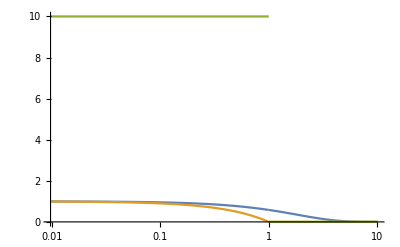

```mathematica
(#-1)y&/@{λexp[y],λflat[y],λsharpMassLike[y,0.1]}
LogLinearPlot[%,{y,0,10}]
```

```mathematica
Inactive[Integrate][y^(d/2-1)((-y^2 λ'[y])/(y(1+r[y])+ω)),{y,0,∞},Assumptions->{d>1,ω>0}]/.{r'[y]->λ'[y],r[y]->λ[y]-1}
%/.{λ'[y]->λflat'[y],λ[y]->λflat[y]}
%//Activate//FullSimplify
```

Integrate[-(y^(1+d/2) λ'[y])/(ω+y λ[y]),{y,0,∞},Assumptions→{d>1,ω>0}]

Integrate[-(y^(1+d/2) (-((-1+1/y) DiracDelta[-1+y])-HeavisideTheta[1-y]/y^2))/(ω+y (1+(-1+1/y) HeavisideTheta[1-y])),{y,0,∞},Assumptions→{d>1,ω>0}]

2/(d+d ω)

```mathematica
AsymptoticIntegrate[-(y^(1+d/2) {-DiracDelta[-1+y]/(y ϵ),-HeavisideTheta[1-y]/(y^2 ϵ)})/(ω+y (1+HeavisideTheta[1-y]/(y ϵ))),{y,0,∞},ϵ->0,Assumptions->{d>1,ω>0}]//Activate
Series[%,{ϵ,0,1}]
```

{-(ϵ (1+ω))/HeavisideTheta[0]^2+1/HeavisideTheta[0],2/d+2 ϵ (-1/(2+d)-ω/d)}

{1/HeavisideTheta[0]+((-1-ω) ϵ)/HeavisideTheta[0]^2+O[ϵ]^2,2/d+2 (-1/(2+d)-ω/d) ϵ+O[ϵ]^2}

```mathematica
( -√(λflat[p^2/k^2] p^2+Δ^2))/.HeavisideTheta[1-p^2/k^2]->HeavisideTheta[k^2-p^2]
((%/.k->0)-(%/.k->Λ))
Integrate[%,{p,-Λ,Λ},Assumptions->{Δ>0,Λ>0}]
Integrate[%%,{p,-∞,-Λ},Assumptions->{Δ>0,Λ>0}]+Integrate[%%,{p,Λ,∞},Assumptions->{Δ>0,Λ>0}]
Series[%,{Λ,∞,3}]
```

-√(Δ^2+p^2 (1+(-1+k^2/p^2) HeavisideTheta[k^2-p^2]))

-√(Δ^2+p^2 (1-HeavisideTheta[-p^2]))+√(Δ^2+p^2 (1+(-1+Λ^2/p^2) HeavisideTheta[-p^2+Λ^2]))

Λ √(Δ^2+Λ^2)-Δ^2 ArcTanh[Λ/(√(Δ^2+Λ^2))]

0

0

```mathematica
(-√(λsharpMassLike[p^2/k^2,ϵ] p^2+Δ^2))/.HeavisideTheta[1-p^2/k^2]->HeavisideTheta[k^2-p^2]
((%/.k->0)-(%/.k->Λ))
Integrate[%,{p,-Λ,Λ},Assumptions->{Δ>0,Λ>0,ϵ>0}]
Normal[Series[%,{ϵ,0,0}]]//Simplify[#,Assumptions->{Λ>0,ϵ>0}]&//Expand
```

-√(Δ^2+p^2 (1+(k^2 HeavisideTheta[k^2-p^2])/(p^2 ϵ)))

-√(p^2+Δ^2)+√(Δ^2+p^2 (1+(Λ^2 HeavisideTheta[-p^2+Λ^2])/(p^2 ϵ)))

-Λ √(Δ^2+Λ^2)-Δ^2 ArcTanh[Λ/(√(Δ^2+Λ^2))]+(Λ √(ϵ (Δ^2 ϵ+(1+ϵ) Λ^2))+(Δ^2 ϵ+Λ^2) ArcTanh[(ϵ Λ)/(√(ϵ (Δ^2 ϵ+(1+ϵ) Λ^2)))])/ϵ

(2 Λ^2)/(√ϵ)-Λ √(Δ^2+Λ^2)-Δ^2 ArcTanh[Λ/(√(Δ^2+Λ^2))]

```mathematica
(-√(λsharpMomentumLike[p^2/k^2,ϵ] p^2+Δ^2))/.HeavisideTheta[-1+p^2/k^2]->HeavisideTheta[-k^2+p^2]
((%/.k->0)-(%/.k->Λ))
Integrate[%,{p,-2Λ,2Λ},Assumptions->{Δ>0,Λ>0,ϵ>0}]
Normal[Series[%,{ϵ,0,0}]]//Simplify[#,Assumptions->{Λ>0,ϵ>0}]&//Expand
```

-√(Δ^2+p^2/(ϵ+HeavisideTheta[-k^2+p^2]))

-√(Δ^2+p^2/(ϵ+HeavisideTheta[p^2]))+√(Δ^2+p^2/(ϵ+HeavisideTheta[p^2-Λ^2]))

$Aborted

$Aborted

```mathematica
+Δ^2 ArcTanh[(2 Λ)/(√(Δ^2+4 Λ^2))]-Δ^2 Log[Δ/(-2 Λ+√(Δ^2+4 Λ^2))]//TrigToExp//PowerExpand//Simplify[#,Assumptions->{Δ>0,Λ>0,Λ>Δ}]&
%/.Δ->1/.Λ->2.
```

0

0

```mathematica
1/(νμ^2+p^2 λ[p^2/k^2]+Δ^2)(νμ^2-Δ^2+p(p-q)√λ[(p-q)^2/k^2] √λ[p^2/k^2])/(νμ^2+Δ^2+(p-q)^2 λ[(p-q)^2/k^2])/.λ[x_]:>λflat[x]
(%/.k->Λ)-(%/.HeavisideTheta[_]->1)/.HeavisideTheta[x_]:>HeavisideTheta[Λ^2 x//Simplify]
```

(-Δ^2+νμ^2+p (p-q) √(1+(-1+k^2/p^2) HeavisideTheta[1-p^2/k^2]) √(1+(-1+k^2/(p-q)^2) HeavisideTheta[1-(p-q)^2/k^2]))/((Δ^2+νμ^2+p^2 (1+(-1+k^2/p^2) HeavisideTheta[1-p^2/k^2])) (Δ^2+νμ^2+(p-q)^2 (1+(-1+k^2/(p-q)^2) HeavisideTheta[1-(p-q)^2/k^2])))

-(√(k^2/p^2) p √(k^2/(p-q)^2) (p-q)-Δ^2+νμ^2)/((k^2+Δ^2+νμ^2)^2)+(-Δ^2+νμ^2+p (p-q) √(1+(-1+Λ^2/p^2) HeavisideTheta[-p^2+Λ^2]) √(1+(-1+Λ^2/(p-q)^2) HeavisideTheta[-p^2+2 p q-q^2+Λ^2]))/((Δ^2+νμ^2+p^2 (1+(-1+Λ^2/p^2) HeavisideTheta[-p^2+Λ^2])) (Δ^2+νμ^2+(p-q)^2 (1+(-1+Λ^2/(p-q)^2) HeavisideTheta[-p^2+2 p q-q^2+Λ^2])))

```mathematica
Simplify[%500,Assumptions->{Λ>0,(p-q)^2<Λ^2,p^2<Λ^2}]//Simplify
```

(Δ^2-νμ^2+(k^2 p (-p+q))/(Abs[p] Abs[p-q]))/((k^2+Δ^2+νμ^2)^2)+(-Δ^2+νμ^2+(p (p-q) Λ^2)/(Abs[p] Abs[p-q]))/((Δ^2+Λ^2+νμ^2)^2)

```mathematica
Simplify[%500,Assumptions->{Λ>0,(p-q)^2>Λ^2,p^2>Λ^2}]//Simplify
```

(p^2-p q-Δ^2+νμ^2)/((p^2+Δ^2+νμ^2) ((p-q)^2+Δ^2+νμ^2))+(Δ^2-νμ^2+(k^2 p (-p+q))/(Abs[p] Abs[p-q]))/((k^2+Δ^2+νμ^2)^2)

## C.4. Expansion and computation of the thermodynamic potential

Computations for the App. C.4. “Series expansion for the medium part of the mean-field thermodynamic potential” [M. J. Steil, - 2023 - PhD thesis] and Actor codepackage

[A. Actor, Compactification At Finite Temperature In Noncompact Electrodynamics, Annals Phys. 159 (1985) 445-466 } : [A1]
[A. Actor, Chemical Potentials In Gauge Theories, Phys.Lett. 157B (1985) 53-56}: [A2]
[A. Actor, Zeta Function Regularization of High Temperature Expansions in Field Theory, Nucl.Phys. B265 (1986) 689-719] : [A3]

[M. Abramowitz and I. Stegun, Handbook of Mathematical Functions,  Dover, New York 1970]: [AS70]
[A. Erdélyi et al. , Higher Transcendental Functions, Vol 1, New York 1955]: [E55]
[L. Lewin, Polylogarithms and associated functions, 1981]: [L81]
[https://en.wikipedia.org/wiki/Matsubara_frequency]: [Wiki]

## Bessel Function Series of Ω_F(β,Δ,μ,a=0) : Derivation from [A3, (3.7)] to [A3, (3.11)]

[A. Actor - 1985 - Zeta Function Regularization of High-Temperature Expansions in Field Theory]

-Graphics-, with A_0=-I μ

-Graphics-

s: spatial dimension (=3 in 3+1D)
V: spatial Volume
d=Tr[γ_Id]: Dimension of the spinors (=4 in 3+1D)=dγ
ω^2≡k^2+Δ^2: Energies
a_s: Area of the (s-1) unit sphere a_s≡S_(s-1)=2π^(s/2)/Gamma[s/2] [see e.g.: https://en.wikipedia.org/wiki/N-sphere] 
β=1/T: inverse temperature

```mathematica
Actor`a[s_/;IntegerQ[s]&&s≥1]:=2 π^(s/2)/Gamma[1/2 s]
Row[Table[Row[{Subscript["a",s],"=",Actor`a[s]}],{s,1,3}],",\t"]//CellPrintDisplayFormulaNumbered
```

,	",	"("a")_1"="2("a")_2"="2 π("a")_3"="4 π

Ω_F[β,β Δ,β μ]/V=-(dγ Nf)/2 1/(2π)^s∫_V_s ⅆ^s k  ℳ_(f;th)^0(μ,β;√(k^2+Δ^2))=-d_γ/2 1/(2π)^s∫_0^∞ ⅆ^s k (Log[1+ⅇ^(β (-μ-√(k^2+Δ^2)))]+Log[1+ⅇ^(β (μ-√(k^2+Δ^2)))])

Ω_F[β,β Δ,β μ]/V=-(dγ Nf)/2 a_s/(2π)^s 1/β∫_0^∞ ⅆk k^(-1+s) (Log[1+ⅇ^(-β (√(k^2+Δ^2)-μ))]+Log[1+ⅇ^(-β (√(k^2+Δ^2)+μ))]);

Ω_F≡-(dγ Nf)/2(V T)/(2π)^s∑_± ∫ⅆ^s k Log[1+Exp[-β(ω±μ)]]=-dγ Nf V T^(s+1) a_s∑_(m=1)^∞ (-1)^(m+1)/m^(s+1)f_s[m β Δ]Cosh[m β μ], [A3,(3.11),a=0], where
f_s[m β Δ]≡((m β Δ)/(2π))^s ∫_0^∞ ⅆx x^(s-1)Exp[-m β Δ √(x^2+1)]=Gamma[1/2 s]/(2 π^(s/2))2((m β Δ)/(2π))^((s+1)/2)K_((s+1)/2)[m β Δ]=1/a_s 2((m β Δ)/(2π))^((s+1)/2)K_((s+1)/2)[m β Δ], [A3, (3.12)].

Ω_F[β,β Δ,β μ]/V=-2 d_γ Nf β^(-s-1) ∑_(m=1)^∞ (-1)^(m+1)((β Δ)/(2π m))^((s+1)/2)K_((s+1)/2)[m β Δ]Cosh[m β μ]
=2dγ Nf((2π β)/Δ)^(-1/2-s/2)∑_(m=1)^∞ (-1)^m(1/m)^((s+1)/2)K_((s+1)/2)[m β Δ]Cosh[m β μ]
=2dγ Nf ((2π β)/Δ)^-n∑_(m=1)^∞ (-1)^m(1/m)^n K_n[m β Δ]Cosh[m β μ], n≡(s+1)/2⇒s=2n-1
=2dγ Nf ((2π β)/Δ)^-n∑_(m=1)^∞ (-1)^m(1/m)^n K_n[m β Δ]Cosh[m z],  z≡βμ
=2^(1-n) dγ Nf π^-n y^n β^(-2 n)∑_(m=1)^∞ (-1)^m m^-n BesselK[n,m y] Cosh[m z],  y≡β Δ

Actor`ΩFm=-2 dγ Nf β^(-s-1) (-1)^(m+1)((β Δ)/(2π m))^((s+1)/2)BesselK[(s+1)/2,m β Δ]Cosh[m β μ];
Actor`ΩFmnSplit={2^(1-n) dγ Nf π^-n y^n β^(-2 n),Inactive[Sum][(-1)^m m^-n BesselK[n,m y]Cosh[m z],{m,1,∞}]};
Actor`dΩfdk=-(dγ Nf)/2 1/((2π)^s β)Actor`a[s]k^(s-1)(Log[1+Exp[-β(ω-μ)]]+Log[1+Exp[-β(ω+μ)]])/.ω->√(k^2+Δ^2);

Actor`ΩFm-Times@@(Actor`ΩFmnSplit/.Inactive[Sum][a_,b_]:>a//.n->(s+1)/2)/.z→μ β/.y→Δ β//PowerExpand//Simplify;

ClearAll[Actor`Ωnumeric]
Actor`Ωnumeric[d_:2,s_:1,nf_:1][μ_,T_][Δ_]:=-nf* d/2(Actor`a[s])/(2π)^2*Piecewise[{
	{0.,T≤0&&μ≤0},
	{NIntegrate[With[{ω=Sqrt[k^2+Δ^2]},k^(s-1)(μ-ω)HeavisideTheta[μ-ω]],{k,0,∞}],T≤0},
	{NIntegrate[With[{ω=Sqrt[k^2+Δ^2],β=1./T},Log[1+ⅇ^(-β (ω-μ))]+Log[1+ⅇ^(-β (ω+μ))]],{k,0,∞}],True}},
{μ,T}]/;NumberQ[μ]&&NumberQ[T]&&NumberQ[Δ]

Derivation

Identity  [AS70, (4.1.24)];
Log[1+z]=z-1/2 z^2+1/3 z^3-...=∑_(m=1)^∞ (-1)^(m+1)z^m/m, Abs[z]≤1 and z≠-1

```mathematica
Series[Log[1+z],{z,0,5}];
Sum[z^m(-1)^(m+1)/m,{m,1,5}];
```

Identity  [AS70, (9.6.23)]; for BesselK[ν,z]
K_ν[z]=(π^(1/2)(1/2 z)^ν)/Gamma[ν+1/2]∫_0^∞ ⅆt Sinh[t]^(2ν)Exp[-z Cosh[t]]=π^(ν+1/2)/Gamma[ν+1/2](z/(2π))^ν∫_0^∞ ⅆt Sinh[t]^(2ν)Exp[-z Cosh[t]]=(π^(1/2)(1/2 z)^ν)/Gamma[ν+1/2]∫_1^∞ ⅆs Exp[-z s](s^2-1)^(ν-1/2), s≡Cosh[t];Re[ν]>1/2 and Abs[Arg[z]]<1/2 π

```mathematica
1/e(nf[(e+μ)/T]+nf[(e-μ)/T])/.e->√(p^2+Δ^2)/.nf`expRule
NIntegrate[%/.{T->0.1,μ->0,Δ->0.1},{p,0,∞}]
```

(1/(1+ⅇ^((√(p^2+Δ^2)-μ)/T))+1/(1+ⅇ^((√(p^2+Δ^2)+μ)/T)))/(√(p^2+Δ^2))

```mathematica
D[Cosh[t],t];
Solve[Cosh[t]^2-Sinh[t]^2==1/.{Cosh[t]->s,Sinh[t]->sinh},sinh];
(π^(1/2)(1/2 z)^ν)/Gamma[ν+1/2] Integrate[ Exp[-z t](t^2-1)^(ν-1/2),{t,1,∞},Assumptions->{Re[ν]>1/2 , Abs[Arg[z]]<1/2 π}];
```

Ω_F≡-d/2(V T)/(2π)^s∑_± ∫ⅆ^s k Log[1+Exp[-β(ω±μ)]]
=-d/2(V T)/(2π)^s a_s∑_± ∑_(m=1)^∞ ∫_0^∞ ⅆk k^(s-1) (-1)^(m+1)Exp[-β(ω±μ)]^m/m;ⅆ^s k =a_s ⅆk k^(s-1), using [AS70, (4.1.24)]
=-d/2(V T)/(2π)^s a_s∑_± ∑_(m=1)^∞ ∫_0^∞ ⅆk k^(s-1) (-1)^(m+1)/m Exp[-m β ω](∑_± Exp[∓m β μ]);
=-d(V T)/(2π)^s a_s ∑_(m=1)^∞ (Δ^(1+s-1))∫_0^∞ ⅆx x^(s-1) (-1)^(m+1)/m Exp[-m β M √(x^2+1)]Cosh[m β μ]; ω=√(k^2+Δ^2)=Δ √(k^2/Δ^2+1), k→Δ x, ∑_± Exp[∓m β μ]= Exp[-m β μ]+Exp[+m β μ]=2 Cosh[m β μ];
=-d V T^(s+1) a_s∑_(m=1)^∞ ((β Δ)/(2π))^s∫_0^∞ ⅆx x^(s-1) (-1)^(m+1)/m Exp[-m β Δ √(x^2+1)]Cosh[m β μ]; 
=-d V T^(s+1) a_s∑_(m=1)^∞ (-1)^(m+1)/m^(s+1)m^(s+1)/m∫_0^∞ ⅆx x^(s-1)((β Δ)/(2π))^s Exp[-m β Δ √(x^2+1)]Cosh[m β μ]; 
=-d V T^(s+1) a_s∑_(m=1)^∞ (-1)^(m+1)/m^(s+1)f_s[m β Δ]Cosh[m β μ], [A3,(3.11),a=0]; f_s[m β M]≡((m β Δ)/(2π))^s ∫_0^∞ ⅆx x^(s-1)Exp[-m β Δ √(x^2+1)];

Identity  [AS70, (9.6.28),k=1];   for BesselK[ν,z]
(1/z d/dz)^1(z^-ν Exp[I π ν]K_ν[z])=z^(-ν-1)Exp[I π (ν+1)]K_(ν+1)[z]
z^(-ν-1)Exp[I π ν]-ν/z K_ν[z]+z^(-ν-1)Exp[I π ν]K_ν'[z]=z^(-ν-1)Exp[I π ν]Exp[I π ]K_(ν+1)[z]
ν/z K_ν[z]-K_ν'[z]=K_(ν+1)[z]

```mathematica
ν z^-1 BesselK[ν,z]-D[BesselK[ν,z],z]-BesselK[1+ν,z]//FullSimplify;
D[BesselK[ν,z] z^-ν Exp[I π ν],z]/z-Exp[I π(ν+1)]BesselK[ν+1,z] z^(-ν-1)//FullSimplify;
```

f_s[z]≡(z/(2π))^s ∫_0^∞ ⅆx x^(s-1)Exp[-z √(x^2+1)], z≡m β Δ ;
=(z/(2π))^s ∫_0^∞ ⅆt Cosh[t]Sinh[t]^(s-1)Exp[-z Cosh[t]]; x≡Sinh[t]: dx/dt=Cosh[t], √(x^2+1)=√(Sinh[t]^2+1)=Cosh[t] for t∈[0,∞],{x→0⇔t→0, x→∞⇔t→∞}
=2^(-1/2-s/2) π^(-1/2-s) (1/z)^(-1/2-s/2) Gamma[s/2]((s-1)/(2z)K_((s-1)/2)[z]-K_((s-1)/2)'[z])      using [AS70, (9.6.23)]
=2^(-1/2-s/2) π^(-1/2-s) (1/z)^(-1/2-s/2) Gamma[s/2]K_((s+1)/2)[z]     using [AS70, (9.6.28),k=1]
=Gamma[1/2 s]/(2 π^(s/2))2(z/(2π))^((s+1)/2)K_((s+1)/2)[z]
=1/a_s 2((m β Δ)/(2π))^((s+1)/2)K_((s+1)/2)[m β Δ ], [A3, (3.12)]

```mathematica
π^(ν+1/2)/Gamma[ν+1/2](z/(2π))^ν Sinh[t]^(2ν)Exp[-z Cosh[t]]
ν/z%-D[%,z]/.ν->(s-1)/2//Simplify
%*(π^(s/2)/Gamma[s/2]((2π)/z)^((s+1)/2))^-1
FullSimplify[%,Assumptions->z>0]
FullSimplify[%/(z/(2π))^s,z>0]
```

```mathematica
2^(-1/2-s/2) π^(-1/2-s) (1/z)^(-1/2-s/2) Gamma[s/2]*(2 π^(s/2)/Gamma[1/2 s])
Simplify[%-2(z/(2π))^((s+1)/2),Assumptions->z>0]
```

## Ascending Series for BesselK[n,z] and Ginzburg Landau expansion for odd s (even s+1)

```mathematica
Row[{"(SubscriptBox[Ω, F][β, y, z])/V"," = ",Row[Actor`ΩFmnSplit,""]}]//CellPrintDisplayFormulaNumbered
```

"(SubscriptBox[Ω, F][β, y, z])/V"" = "2^(1-n) dγ Nf π^-n y^n β^(-2 n)(-1)^m m^-n BesselK[n,m y] Cosh[m z]m1∞

ClearAll[Actor`ΩFnSplit]
Actor`ΩFnSplit[n_,dγ_,Nf_:1][β_:β,z_:z,Δ_:Δ][kmax_,listQ_:False,activeQ_:True]:=Module[{k},{
	(dγ/2^n Nf)*Inactive[Sum][(-1)^k 2^(-1-2 k+n) π^-n((-1-k+n)!)/(k!)(PolyLog[-2 k+2 n,-ⅇ^-z]+PolyLog[-2 k+2 n,-ⅇ^z]) β^(2 k-2 n) Δ^(2 k) ,{k,0,n-1}](*S1*),
	(dγ/2^n Nf)*Inactive[Sum][(-1)^n 2^-n π^-n 1/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/2]+PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z]) Δ^(2 n),{k,1,1}](*S2*),
	(dγ/2^n Nf)*Inactive[Sum][(-1)^n 2^(-2 k-n) π^-n 1/(k! (k+n)!)(PolyLog^(1,0)[-2 k,-ⅇ^-z]+PolyLog^(1,0)[-2 k,-ⅇ^z]) β^(2 k) Δ^(2 (k+n)),{k,1,kmax}](*S4*)
}//If[listQ,Identity,Total]//If[activeQ&&kmax≠∞,Activate,#/.k→j&]]/;(IntegerQ[n]||(!activeQ))

ClearAll[Actor`Ωfα2m]
Actor`Ωfα2m[n_,dγ_,Nf_:1][β_:β,z_:z][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+n) 2^(-1-4 k+3 n) π^(-2 k+n)((-1-k+n)!)/(k!(-2 k+2 n)!)Sum[(-1)^-l (2 π)^(-2 l) BernoulliB[-2 (k+l-n),1/2] Binomial[-2 k+2 n,2 (n-k-l)] z^(2 l) ,{l,0,n-k}]β^(2 k-2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!)(-HarmonicNumber[n]/2+Log[(β Δ)/(4 π)]-Re[PolyGamma[0,1/2+(ⅈ z)/(2 π)]])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^(1+k+n) 2^(-4 k-n) π^(-2 k-n)1/(k! (k+n)!)(Re[PolyGamma[2 k,1/2+(ⅈ z)/(2 π)]]) β^(2 k) (* Δ^(2 (k+n))*)]

]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

Actor`Ωfα2mT0[n_,dγ_,Nf_:1][μ_:μ][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+k) 2^(-1-2 k+n) π^-n ((-1-k+n)!)/(k! (-2 k+2 n)!)μ^(-2 k+2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!) (-HarmonicNumber[n]/2+Log[Δ/(2 μ)])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^n 2^(-2 k-n) π^-n ((-1+2 k)!)/(k! (k+n)!)μ^(-2 k)(* Δ^(2 (k+n))*)]

]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

Actor`Ωfα2mμ0[n_,dγ_,Nf_:1][β_:β][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+n) 2^(-1-4 k+3 n) π^(-2 k+n)((-1-k+n)!)/(k!(-2 k+2 n)!)BernoulliB[-2 k+2 n,1/2]β^(2 k-2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/π])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^(1+n+k) π^(-2 k-n)2^(-2 k-n)(-2+2^(-2 k)) ((2 k)!)/(k! (k+n)!) Zeta[1+2 k]β^(2 k)(* Δ^(2 (k+n))*)]
]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

n=1 and n=2 GL coefficients

see also [A. Ahmed - 2018 - Ginzburg-Landau Type Approach to the 1+1 Gross Neveu Model - Beyond Lowest Non-Trivial Order]

```mathematica
Needs["TeXUtilities`"] (* https://github.com/jkuczm/MathematicaTeXUtilities *)
System`Convert`TeXFormDump`maketex["ⅈ"]="\\iu";
System`Convert`TeXFormDump`maketex["ⅇ"]="\\eu";

ClearAll[RePolyGamma];
RePolyGamma/:Format[RePolyGamma[n_,x_],TeXForm]:=TeXVerbatim["\\Re\\psi^{("<>ToString[n,TeXForm]<>")}("<>StringReplace[ToString[x,TeXForm],"\\frac"->"\\tfrac"]<>")"]
```

```mathematica
n=1;dγ=2;Nf=1;
{{Subscript["α",0],Expand[Ωfβ2m[n,dγ,Nf][1/T,μ/T][][0]]}};
Table[{Subscript["α",2m],Piecewise[{{Ωfβ2m[n,dγ,Nf][1/T,μ/T][][m],T>0&&μ>0},{Ωfβ2mμ0[n,dγ,Nf][1/T][][m],T>=0&&μ==0},{Ωfβ2mT0[n,dγ,Nf][μ][][m],T==0&&μ>=0}}]},{m,1,3}];

(*Mathematica Output*)
Column[{"d=1, d_γ=2, N=1:",Row[#,"(μ,T)="]&/@Flatten[{%%,%},1]}//Flatten]//CellPrintDisplayFormulaNumbered

(*TeX Output*)
StringJoin["\\alpha_"<>ToString[#[[1,2]],TeXForm],"(μ,T)"," &= ",ToString[#[[2]],TeXForm],"\, ,", "\\\\"]&/@(Flatten[{%%%,%%},1]/.Re[PolyGamma[n_,x_]]:>RePolyGamma[n,x]);
StringRiffle[%,"\n"];
StringReplace[%,{RegularExpression["& T"]:>"&\\text{for}\\quad T","\\gamma"->"\\gammau","\\frac"->"\\tfrac","\\left"->"","\\right"->"","\\pi"->"\\piu"}];
%//CopyToClipboard;

ClearAll[n,dγ,Nf]
```

"d=1, d_γ=2, N=1:"
(μ,T)="(μ,T)="("α")_0-(π T^2)/6-μ^2/(2 π)
(μ,T)="(μ,T)="("α")_2Piecewise[{{-(-1/2+Log[Δ/(4 π T)]-Re[PolyGamma[0,1/2+(ⅈ μ)/(2 π T)]])/(2 π), T>0&&μ>0}, {-(-1/2+EulerGamma+Log[Δ/(π T)])/(2 π), T≥0&&μ==0}, {-(-1/2+Log[Δ/(2 μ)])/(2 π), T==0&&μ≥0}, {0, True}}]
(μ,T)="(μ,T)="("α")_4Piecewise[{{-Re[PolyGamma[2,1/2+(ⅈ μ)/(2 π T)]]/(64 π^3 T^2), T>0&&μ>0}, {(7 Zeta[3])/(32 π^3 T^2), T≥0&&μ==0}, {-1/(16 π μ^2), T==0&&μ≥0}, {0, True}}]
(μ,T)="(μ,T)="("α")_6Piecewise[{{Re[PolyGamma[4,1/2+(ⅈ μ)/(2 π T)]]/(6144 π^5 T^4), T>0&&μ>0}, {-(31 Zeta[5])/(256 π^5 T^4), T≥0&&μ==0}, {-1/(64 π μ^4), T==0&&μ≥0}, {0, True}}]

```mathematica
n=2;dγ=4;Nf=1;
{{Subscript["α",0],Expand[Ωfβ2m[n,dγ,Nf][1/T,μ/T][][0]]},{Subscript["α",2],Expand[Ωfβ2m[n,dγ,Nf][1/T,μ/T][][1]]}};
Table[{Subscript["α",2m],Piecewise[{{Ωfβ2m[n,dγ,Nf][1/T,μ/T][][m],T>0&&μ>0},{Ωfβ2mμ0[n,dγ,Nf][1/T][][m],T>=0&&μ==0},{Ωfβ2mT0[n,dγ,Nf][μ][][m],T==0&&μ>=0}}]},{m,2,3}];

(*Mathematica Output*)
Column[{"d=1, d_γ=4, N=1:",Row[#,"(μ,T)="]&/@Flatten[{%%,%},1]}//Flatten]//CellPrintDisplayFormulaNumbered

(*TeX Output*)
StringJoin["\\alpha_"<>ToString[#[[1,2]],TeXForm],"(μ,T)"," &= ",ToString[#[[2]],TeXForm],"\, ,", "\\\\"]&/@(Flatten[{%%%,%%},1]/.Re[PolyGamma[n_,x_]]:>RePolyGamma[n,x]);
StringRiffle[%,"\n"];
StringReplace[%,{RegularExpression["& T"]:>"&\\text{for}\\quad T","\\gamma"->"\\gammau","\\frac"->"\\tfrac","\\left"->"","\\right"->"","\\pi"->"\\piu"}];
%//CopyToClipboard;

ClearAll[n,dγ,Nf]
```

"d=1, d_γ=4, N=1:"
(μ,T)="(μ,T)="("α")_0-7/180 π^2 T^4-(T^2 μ^2)/6-μ^4/(12 π^2)
(μ,T)="(μ,T)="("α")_2T^2/12+μ^2/(4 π^2)
(μ,T)="(μ,T)="("α")_4Piecewise[{{(-3/4+Log[Δ/(4 π T)]-Re[PolyGamma[0,1/2+(ⅈ μ)/(2 π T)]])/(8 π^2), T>0&&μ>0}, {(-3/4+EulerGamma+Log[Δ/(π T)])/(8 π^2), T≥0&&μ==0}, {(-3/4+Log[Δ/(2 μ)])/(8 π^2), T==0&&μ≥0}, {0, True}}]
(μ,T)="(μ,T)="("α")_6Piecewise[{{Re[PolyGamma[2,1/2+(ⅈ μ)/(2 π T)]]/(384 π^4 T^2), T>0&&μ>0}, {-(7 Zeta[3])/(192 π^4 T^2), T≥0&&μ==0}, {1/(96 π^2 μ^2), T==0&&μ≥0}, {0, True}}]

Derivation PolyLog derivative form

Identity  [AS70, (9.6.11)];   Ascending  Series for BesselK[n,x] for integer n
BesselK[n,x]=1/2(1/2 x)^-n∑_(k=0)^(n-1) ((n-k-1)!)/(k!)(-1/4 x^2)^k+(-1)^(n+1)(Log[x]-Log[2])(1/2 x)^n∑_(k=0)^∞ ((1/4 x^2)^k)/(k! Gamma[n+k+1])+(-1)^n 1/2(1/2 x)^n∑_(k=0)^∞ (PolyGamma[0,k+1]+PolyGamma[0,n+k+1])((1/4 x^2)^k)/(k!(n+k)!)
=∑_(k=0)^(n-1) (-1)^k(2)^(1-n)((n-k-1)!)/(k!)(1/4)^k x^(2k-n)+(2^(-1-n) (-1)^n (-2 EulerGamma+HarmonicNumber[n]+Log[4]-2 Log[x]))/(n!)x^n+∑_(k=1)^∞ ((-1)^(1+n) 2^(-2 k-n))/(k! (k+n)!) Log[x]x^(2 k+n)+∑_(k=1)^∞ ((-1)^n 2^(-1-2 k-n)  (-2 EulerGamma+HarmonicNumber[k]+HarmonicNumber[k+n]+Log[4]))/(k! (k+n)!)x^(2k+n)=S_1^n[x]+S_1^n[x]+S_1^n[x]+S_1^n[x]

```mathematica
ClearAll[BesselKSeriesCoefNew]
BesselKSeriesCoefNew[n_,x_][kmax_,listQ_:False,activeQ_:True]:=Module[{k},{
	Inactive[Sum][(-1)^k 2^(-1-2 k+n)((n-k-1)!)/(k!)x^(2k-n),{k,0,n-1}],(*S1*)
	(2^(-1-n) (-1)^n (-2 EulerGamma+HarmonicNumber[n]+Log[4]-2 Log[x]))/(n!)x^n,(*S2*)
	Inactive[Sum][((-1)^n 2^(-1-2 k-n)  (-2 EulerGamma+HarmonicNumber[k]+HarmonicNumber[k+n]+Log[4]))/(k! (k+n)!)x^(2k+n),{k,1,kmax}],(*S3*)
	Inactive[Sum][((-1)^(1+n) 2^(-2 k-n) Log[x])/(k! (k+n)!) x^(2 k+n),{k,1,kmax}](*S4*)
}//If[listQ,Identity,Total]//If[activeQ&&kmax≠∞,Activate,Identity]]/;IntegerQ[n]||!activeQ
```

⇒∑_(m=1)^∞ (-1)^m m^-n BesselK[n,m y] Cosh[m z]=∑_(m=1)^∞ (-1)^m(1/m)^n(S_1^n[m y]+S_2^n[m y]+S_3^n[m y]+S_4^n[m y])Cosh[m z];

```mathematica
ClearAll[ΩFnSplit]
ΩFnSplit[n_][β_:β,z_:z,Δ_:Δ][kmax_,listQ_:False,activeQ_:True]:=Module[{k},{
	(dγ/2^n Nf)*Inactive[Sum][(-1)^k 2^(-1-2 k+n) π^-n((-1-k+n)!)/(k!)(PolyLog[-2 k+2 n,-ⅇ^-z]+PolyLog[-2 k+2 n,-ⅇ^z]) β^(2 k-2 n) Δ^(2 k) ,{k,0,n-1}](*S1*),
	(dγ/2^n Nf)*Inactive[Sum][(-1/(2 π))^n 1/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/2]+Derivative[1,0][PolyLog][0,-ⅇ^-z]+Derivative[1,0][PolyLog][0,-ⅇ^z]) Δ^(2 n),{k,1,1}](*S2*),
	(dγ/2^n Nf)*Inactive[Sum][2^(-2 k-n) (-1/π)^n 1/(k! (k+n)!)(Derivative[1,0][PolyLog][-2 k,-ⅇ^-z]-Derivative[1,0][PolyLog][-2 k,-ⅇ^z]) β^(2 k) Δ^(2 (k+n)),{k,1,kmax}](*S4*)
}//If[listQ,Identity,Total]//If[activeQ&&kmax≠∞,Activate,#/.k->j&]]/;(IntegerQ[n]||(!activeQ))
```

```mathematica
Row[{"(SubscriptBox[Ω, F][β, y, z])/V"," = ",Row[ΩFnSplit[n][β,z,Δ][∞,True,False]/.j->k,"+"]}]//CellPrintDisplayFormulaNumbered
```

"(SubscriptBox[Ω, F][β, y, z])/V"" = "+"+"2^-n dγ Nf ((-1)^k 2^(-1-2 k+n) π^-n β^(2 k-2 n) Δ^(2 k) (-1-k+n)! (PolyLog[-2 k+2 n,-ⅇ^-z]+PolyLog[-2 k+2 n,-ⅇ^z]))/(k!)k0-1+n2^-n dγ Nf ((-1/(2 π))^n Δ^(2 n) (EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/2]+PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z]))/(n!)k112^-n dγ Nf (2^(-2 k-n) (-1/π)^n β^(2 k) Δ^(2 (k+n)) (PolyLog^(1,0)[-2 k,-ⅇ^-z]-PolyLog^(1,0)[-2 k,-ⅇ^z]))/(k! (k+n)!)k1∞

Auxiliary calculation: Polylogarithms

PolyLog[k,x]=∑_(m=1)^∞ x^m/m^k,  [E55, 1.11.(14)]
⇒∑_(m=1)^∞ (-1)^m m^k ⅇ^(±m z)=∑_(n=1)^∞ ((-ⅇ^(±z))^m)/m^-k=PolyLog[-k,-ⅇ^(±z)]
⇒∑_(m=1)^∞ (-1)^m m^k ⅇ^(±m z) Log[m]=-D[∑_(m=1)^∞ ((-ⅇ^(±z))^m)/m^x ,x]_(x=-k)=-D[PolyLog[l,-ⅇ^(±z)] ,l]_(l=-k)=-PolyLog^(1,0)[-k,-ⅇ^(±z)]
⇒PolyLog[0,x]=∑_(m=1)^∞ x^m=-x/(-1+x)⇒PolyLog[0,1/x]=1/(-1+x)⇒PolyLog[0,x]+PolyLog[0,1/x]=-1

∀k>0: PolyLog[-2 k,z]+PolyLog[-2 k,1/z]=0 [E55, 1.11.(17)]
PolyLog[0,z]+PolyLog[0,1/z]=-1

∑_(m=1)^∞ (-1)^m(1/m)^n Cosh[m z]m^k=1/2∑_(m=1)^∞ (-1)^m(ⅇ^(+z)+ⅇ^-z)m^(k-n)=1/2 (PolyLog[n-k,-ⅇ^-z]+PolyLog[n-k,-ⅇ^z])
∑_(m=1)^∞ (-1)^m(1/m)^n Cosh[m z]m^k Log[m]=1/2∑_(m=1)^∞ (-1)^m(1/m)^n(ⅇ^(+z)+ⅇ^-z)m^k Log[m]=-1/2 (PolyLog^(1,0)[n-k,-ⅇ^-z]+PolyLog^(1,0)[n-k,-ⅇ^z])

Auxiliary calculation: Partial sums

ΩFmnSplit[[2]]
BesselKSeriesCoefNew[n,m y][∞,True,False][[1]]
%%/.BesselK[n_,z_]:>%/.(m y)^n_:>m^n(y)^n//.Inactive[Sum][x_,y_]:>x
Sum[%,{m,1,∞}];
Sum[%,{k,0,n-1}]

∑_(m=1)^∞ (-1)^m m^-n S_1^n[m y]Cosh[m z]=∑_(m=1)^∞ (-1)^m(m)^-n∑_(k=0)^(n-1) ((-1)^k 2^(-1-2 k+n) (m y)^(2 k-n) (-1-k+n)!)/(k!)Cosh[m z]=∑_(k=0)^(n-1) ((-1)^k 2^(-1-2 k+n) y^(2 k-n) (-1-k+n)!)/(k!)∑_(m=1)^∞ (-1)^m m^(2 k-2n) Cosh[m z]
=∑_(k=0)^(n-1) ((-1)^k 2^(-2-2 k+n) y^(2 k-n) (-1-k+n)!)/(k!)(PolyLog[2n-2k,-ⅇ^-z]+PolyLog[2n-2k,-ⅇ^z])

ΩFmnSplit[[2]]
BesselKSeriesCoefNew[n,m y][∞,True,False][[2]]
%%/.BesselK[n_,z_]:>%/.(m y)^n_:>m^n(y)^n//.Inactive[Sum][x_,y_]:>x
Sum[%,{m,1,∞}]/.Derivative[0,1,0][LerchPhi][x_,n_,1]:>Derivative[1,0][PolyLog][n,x]/x//FunctionExpand//FullSimplify[#,Assumptions→{n>0,n∈Integers}]&;
%/(2^(-1-n) (-y)^n)/(n!)/.PolyLog^(1,0)[0,-Cosh[z]+Sinh[z]]:>PolyLog^(1,0)[0,-Exp[-z]]//Simplify

∑_(m=1)^∞ (-1)^m m^-n S_2^n[m y]Cosh[m z]=∑_(m=1)^∞ (-1)^m(m)^-n((-1)^n 2^(-1-n) (m y)^n (-2 EulerGamma+HarmonicNumber[n]+Log[4]-2 Log[m y]))/(n!)Cosh[m z]=((-1)^n 2^(-1-n) y^n)/(n!)∑_(m=1)^∞ (-1)^m(-2 EulerGamma+HarmonicNumber[n]+Log[4]-2 Log[m y])Cosh[m z] 
=((-1)^n 2^(-1-n) (y)^n)/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[y/2]+PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z])

ΩFmnSplit[[2]]
BesselKSeriesCoefNew[n,m y][∞,True,False][[3]]
%%/.BesselK[n_,z_]:>%/.(m y)^n_:>m^n(y)^n//.Inactive[Sum][x_,y_]:>x
Sum[%,{m,1,∞}]/.Derivative[0,1,0][LerchPhi][x_,n_,1]:>Derivative[1,0][PolyLog][n,x]/x//FunctionExpand//FullSimplify[#,Assumptions→{n>0,n∈Integers}]&;
%//.PolyLog[-2k,-Cosh[z]+Sinh[z]]:>PolyLog[-2k,-Exp[-z]]/.Gamma[x_+1]:>x!//Simplify

∑_(m=1)^∞ (-1)^m m^-n S_3^n[m y]Cosh[m z]=∑_(m=1)^∞ (-1)^m(m)^-n∑_(k=1)^∞ ((-1)^n 2^(-1-2 k-n) (m y)^(2 k+n) (-2 EulerGamma+HarmonicNumber[k]+HarmonicNumber[k+n]+Log[4]))/(k! (k+n)!)Cosh[m z]=∑_(k=1)^∞ ((-1)^n 2^(-1-2 k-n) y^(2 k+n) (-2 EulerGamma+HarmonicNumber[k]+HarmonicNumber[k+n]+Log[4]))/(k! (k+n)!)∑_(m=1)^∞ (-1)^m(m)^(2k)Cosh[m z]
=∑_(k=0)^(n-1) (-1)^n 2^(-2-2 k-n) y^(2 k+n)(-2 EulerGamma+HarmonicNumber[k]+HarmonicNumber[k+n]+Log[4])/(k! (k+n)!)(PolyLog[2n-2k,-ⅇ^-z]+PolyLog[2n-2k,-ⅇ^z])
=0, since PolyLog[-2 k,z]+PolyLog[-2 k,1/z]=0 [E55, 1.11.(17)]

ΩFmnSplit[[2]]
BesselKSeriesCoefNew[n,m y][∞,True,False][[4]]
%%/.BesselK[n_,z_]:>%/.(m y)^n_:>m^n(y)^n//.Inactive[Sum][x_,y_]:>x
Sum[%,{m,1,∞}]/.Derivative[0,1,0][LerchPhi][x_,n_,1]:>Derivative[1,0][PolyLog][n,x]/x//FunctionExpand//FullSimplify[#,Assumptions→{n>0,n∈Integers}]&;
%//.PolyLog[-2k,-Cosh[z]+Sinh[z]]:>PolyLog[-2k,-Exp[-z]]/.Gamma[x_+1]:>x!/.PolyLog^(1,0)[-2k,-Cosh[z]+Sinh[z]]:>PolyLog^(1,0)[-2k,-Exp[-z]]//Simplify

∑_(m=1)^∞ (-1)^m m^-n S_4^n[m y]Cosh[m z]=∑_(m=1)^∞ (-1)^m(m)^-n∑_(k=1)^∞ ((-1)^(1+n) 2^(-2 k-n) (m y)^(2 k+n) Log[m y])/(k! (k+n)!)Cosh[m z]=∑_(k=1)^∞ ((-1)^(1+n) 2^(-2 k-n) y^(2 k+n))/(k! (k+n)!)∑_(m=1)^∞ (-1)^m(m)^(2k)(Log[m]+Log[y])Cosh[m z]=∑_(k=1)^∞ ((-1)^(1+n) 2^(-1-2 k-n) y^(2 k+n))/(k! (k+n)!)(Log[y] (PolyLog[-2 k,-ⅇ^-z]+PolyLog[-2 k,-ⅇ^z])-PolyLog^(1,0)[-2 k,-ⅇ^-z]-PolyLog^(1,0)[-2 k,-ⅇ^z])
=∑_(k=1)^∞ ((-1)^n 2^(-1-2 k-n) y^(2 k+n))/(k! (k+n)!)(PolyLog^(1,0)[-2 k,-ⅇ^-z]-PolyLog^(1,0)[-2 k,-ⅇ^z])

### PolyGamma and PolyLog relations

see also [Blinnikov1988Sep: S. I. Blinnikov and M. A. Rudzskii - 1989 - New Representations of the thermodynamic functions of Fermi gases] ← [A. Ahmed - 2018 - Ginzburg-Landau Type Approach to the 1+1 Gross Neveu Model - Beyond Lowest Non-Trivial Order]

Actor`DLiPolyGammaRule=PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[ n_,-ⅇ^z_]:>0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^(-1+n) π^n (PolyGamma[-n,(π-ⅈ z)/(2 π)]+PolyGamma[-n,(π+ⅈ z)/(2 π)]);
Actor`DLiRePolyGammaRule=PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[ n_,-ⅇ^z_]:>0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^n π^n Re@PolyGamma[-n,(π+ⅈ z)/(2 π)];
Actor`DLiRePolyGammaRuleExplizit[n_,z_]:=PolyLog^(1,0)[n,-ⅇ^z]->0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^n π^n Re@PolyGamma[-n,(π+ⅈ z)/(2 π)]-+PolyLog^(1,0)[ n,-ⅇ^-z];
Actor`RePolyGammaToPolyGammaSum=Re@PolyGamma[n_,x_]:>1/2 (PolyGamma[n,x]+PolyGamma[n,ComplexExpand@Conjugate[x]]);
Actor`DLiRePolyGammaInvRule=Re@PolyGamma[n_,(π+ⅈ z_)/(2 π)]:>(PolyLog^(1,0)[-n,-ⅇ^-z]+PolyLog^(1,0)[ -n,-ⅇ^z]-0,n/2 (-EulerGamma-Log[2 π]))/((-1)^(1+n/2) 2^-n π^-n);
Actor`PolyLogBernoulliBRule=PolyLog[n_,-ⅇ^-z]:>-PolyLog[n,-ⅇ^z]-(z^(2 l)(-1)^(-l+n/2) (2 π)^(-2 l+n) BernoulliB[-2 l+n,1/2] Binomial[n,-2 l+n]l0n/2)/(n!);

```mathematica
Derivative[1,0][PolyLog][-2n,-ⅇ^-z]+Derivative[1,0][PolyLog][ -2n,-ⅇ^z];
Row[{"DLi_(2  n)[z] = ",%," = ",%/.Actor`DLiPolyGammaRule}]//CellPrintDisplayFormulaNumbered
```

"DLi_(2  n)[z] = "PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]" = "0,n (-EulerGamma-Log[2 π])+(-1)^(1+n) 2^(-1-2 n) π^(-2 n) (PolyGamma[2 n,(π-ⅈ z)/(2 π)]+PolyGamma[2 n,(π+ⅈ z)/(2 π)])

```mathematica
Derivative[1,0][PolyLog][-2n,-ⅇ^-z]+Derivative[1,0][PolyLog][ -2n,-ⅇ^z];
Row[{"DLi_(2  n)[z] = ",%," = ",%/.Actor`DLiRePolyGammaRule}]//CellPrintDisplayFormulaNumbered
```

"DLi_(2  n)[z] = "PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]" = "0,n (-EulerGamma-Log[2 π])+(-1)^(1+n) (2 π)^(-2 n) Re[PolyGamma[2 n,(π+ⅈ z)/(2 π)]]

```mathematica
PolyLog[2n,-ⅇ^-z]+PolyLog[2 n,-ⅇ^z];
Row[{%," = ", %/.Actor`PolyLogBernoulliBRule}]//CellPrintDisplayFormulaNumbered
```

PolyLog[2 n,-ⅇ^-z]+PolyLog[2 n,-ⅇ^z]" = "-((-1)^(-l+n) (2 π)^(-2 l+2 n) z^(2 l) BernoulliB[-2 l+2 n,1/2] Binomial[2 n,-2 l+2 n]l0n)/((2 n)!)

Proof

(-1)^s PolyLog[s,1/x]+PolyLog[s,x]==((2 π I)^s HurwitzZeta[1-s,1/2+Log[-x]/(2 π ⅈ)])/Gamma[s] [2010.09860,(4.6)] holds for real x<0
⇒(-1)^(2 n) PolyLog[2 n,-ⅇ^-z]+PolyLog[2 n,-ⅇ^z]=((2 ⅈ π)^(2 n) HurwitzZeta[1-2 n,(π-ⅈ z)/(2 π)])/Gamma[2 n], x=-Exp[z],s=2n,n>0
⇒ⅈ (-1)^(-2 n) π PolyLog[-2 n,-ⅇ^-z]+(-1)^(-2 n) PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]==((2 ⅈ π)^(-2 n) HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)] Log[2 ⅈ π])/Gamma[-2 n]-((2 ⅈ π)^(-2 n) HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)] PolyGamma[0,-2 n])/Gamma[-2 n]-((2 ⅈ π)^(-2 n) HurwitzZeta^(1,0)[1+2 n,(π-ⅈ z)/(2 π)])/Gamma[-2 n], x=-Exp[z],s=2n

```mathematica
{(-1)^s PolyLog[s,1/x]+PolyLog[s,x],((2 π I)^s HurwitzZeta[1-s,1/2+Log[-x]/(2 π ⅈ)])/Gamma[s]};
DLiRePolyGammaProof`id0=Simplify[%/.s->2n/.x->-Exp[z],Assumptions->z>0]//Expand;
DLiRePolyGammaProof`id1=Simplify[D[%%,s]/.s->-2n/.x->-Exp[z],Assumptions->z>0]//Expand;
```

DLi_0[z]=PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z] proof

```mathematica
DLiRePolyGammaProof`n0Rules=MapThread[{#1->Series[#,{n,0,#2}],#3}&,{{PolyGamma[0,-2 n],1/Gamma[-2 n],HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)],Derivative[1,0][HurwitzZeta][1+2 n,(π-ⅈ z)/(2 π)]},{0,1,0,0},{"\t[AS70, 6.3.16]","\t[AS70, 6.1.34]","\t[Berndt1972] Laurent series around its simple pole",""}}];
CellPrintDisplayFormulaNumbered[Column[Row/@%]]
```

PolyGamma[0,-2 n]→1/(2 n)-EulerGamma+O[n]^1"	[AS70, 6.3.16]"
1/Gamma[-2 n]→-2 n+O[n]^2"	[AS70, 6.1.34]"
HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)]→1/(2 n)-PolyGamma[0,(π-ⅈ z)/(2 π)]+O[n]^1"	[Berndt1972] Laurent series around its simple pole"
HurwitzZeta^(1,0)[1+2 n,(π-ⅈ z)/(2 π)]→-1/(4 n^2)-StieltjesGamma[1,(π-ⅈ z)/(2 π)]+O[n]^1""

```mathematica
DLiRePolyGammaProof`id10a=DLiRePolyGammaProof`id1/.Normal[DLiRePolyGammaProof`n0Rules[[All,1]]]//Simplify//Expand;
Row[{"⇒",%[[1]],"O[n]^1"},"+"]==Row[{%[[2]],"O[n]^1"},"+"]//CellPrintDisplayFormulaNumbered
```

+"+""⇒"ⅈ (-1)^(-2 n) π PolyLog[-2 n,-ⅇ^-z]+(-1)^(-2 n) PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]"O[n]^1"==+"+"-EulerGamma (2 ⅈ π)^(-2 n)-(2 ⅈ π)^(-2 n) Log[2 ⅈ π]+2^(1-2 n) EulerGamma n (ⅈ π)^(-2 n) PolyGamma[0,(π-ⅈ z)/(2 π)]-(2 ⅈ π)^(-2 n) PolyGamma[0,(π-ⅈ z)/(2 π)]+2^(1-2 n) n (ⅈ π)^(-2 n) Log[2 ⅈ π] PolyGamma[0,(π-ⅈ z)/(2 π)]-2^(1-2 n) n (ⅈ π)^(-2 n) StieltjesGamma[1,(π-ⅈ z)/(2 π)]"O[n]^1"

```mathematica
DLiRePolyGammaProof`id10b=DLiRePolyGammaProof`id10a/.n->0//FunctionExpand;
Row[{"n=0: ",%[[1]]},""]==Row[{%[[2]]},"+"]//CellPrintDisplayFormulaNumbered
```

"n=0: "-(ⅈ ⅇ^-z π)/(1+ⅇ^-z)+PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z]==+"+"-EulerGamma-(ⅈ π)/2-Log[2]-Log[π]-PolyGamma[0,1/2-(ⅈ z)/(2 π)]

PolyGamma[0,1/2-(ⅈ z)/(2 π)]=-(ⅈ (-1+ⅇ^z) π)/(2 (1+ⅇ^z))+Re[PolyGamma[0,1/2-(ⅈ z)/(2 π)]] [AS70,(6.3.12)]
=-(ⅈ (-1+ⅇ^z) π)/(2 (1+ⅇ^z))+1/2(PolyGamma[0,1/2+(ⅈ z)/(2 π)]+PolyGamma[0,1/2-(ⅈ z)/(2 π)]) [AS70,6.3.9]

```mathematica
DLiRePolyGammaProof`id10b+(ⅈ ⅇ^-z π)/(1+ⅇ^-z)/.PolyGamma[0,1/2-(ⅈ z)/(2 π)]->-(ⅈ (-1+ⅇ^z) π)/(2 (1+ⅇ^z))+Re[PolyGamma[0,1/2-(ⅈ z)/(2 π)]] //Simplify;
Row[{"n=0: ",%[[1]]},""]==Row[{%[[2]],%[[2]]/.Re[PolyGamma[0,(π-ⅈ z)/(2 π)]]->1/2(PolyGamma[0,(π+ⅈ z)/(2 π)]+PolyGamma[0,(π-ⅈ z)/(2 π)]) },"="]//CellPrintDisplayFormulaNumbered
```

"n=0: "PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z]==="="-EulerGamma+Log[1/(2 π)]-Re[PolyGamma[0,(π-ⅈ z)/(2 π)]]-EulerGamma+Log[1/(2 π)]+1/2 (-PolyGamma[0,(π-ⅈ z)/(2 π)]-PolyGamma[0,(π+ⅈ z)/(2 π)])

DLi_(2n)[z]=PolyLog^(1,0)[-2n,-ⅇ^-z]+PolyLog^(1,0)[-2n,-ⅇ^z], n>0 proof

```mathematica
DLiRePolyGammaProof`gammaReflectionRules={Gamma[z_]:>π/Sin[π z]/Gamma[1-z],PolyGamma[0,z_]:>PolyGamma[0,1-z]-π Cot[π z]};
{{Gamma[-2n]->(Gamma[-2n]/.%),"\t [AS70, 6.1.17] Euler's reflection formula"},{PolyGamma[0,-2n]->(PolyGamma[0,-2n]/.%),"\t [AS70, 6.3.7] Euler's reflection formula"}};
Column[Row/@%]//CellPrintDisplayFormulaNumbered
```

Gamma[-2 n]→-(π Csc[2 n π])/Gamma[1+2 n]"	 [AS70, 6.1.17] Euler's reflection formula"
PolyGamma[0,-2 n]→π Cot[2 n π]+PolyGamma[0,1+2 n]"	 [AS70, 6.3.7] Euler's reflection formula"

```mathematica
DLiRePolyGammaProof`id1/.DLiRePolyGammaProof`gammaReflectionRules//Expand;
DLiRePolyGammaProof`id1na=Simplify[%,Assumptions->{n>1,n∈Integers}];
Row[{"n>0: ",%[[1]]},""]==Row[{%[[2]]},"+"]//CellPrintDisplayFormulaNumbered
```

"n>0: "ⅈ π PolyLog[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]==+"+"(2 ⅈ π)^(-2 n) Gamma[1+2 n] HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)]

```mathematica
DLiRePolyGammaProof`hurwitzZetaPolyGammaRule=HurwitzZeta[n_,x_]:>((-1)^n PolyGamma[n-1,x])/((n-1)!);
HurwitzZeta[2n+1,(π-ⅈ z)/(2 π)];
Row[{"∀ n=1,2,... ",%,"=",%/.%%,"\t[NIST, 25.11.12]"}]//CellPrintDisplayFormulaNumbered
```

"∀ n=1,2,... "HurwitzZeta[1+2 n,(π-ⅈ z)/(2 π)]"="((-1)^(1+2 n) PolyGamma[2 n,(π-ⅈ z)/(2 π)])/((2 n)!)"	[NIST, 25.11.12]"

```mathematica
DLiRePolyGammaProof`id1na/.DLiRePolyGammaProof`hurwitzZetaPolyGammaRule/.Gamma[1+2 n]->(2n)!;
FullSimplify[%[[2]],Assumptions->n>0&&n∈Integers];
Row[{"n>0: ",%%[[1]]," = ",%/.(2 ⅈ π)^(-2 n) ->(-1)^(-1-n) (2 π)^(-2 n)}]//CellPrintDisplayFormulaNumbered
```

"n>0: "ⅈ π PolyLog[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]" = "(-1)^-n (2 π)^(-2 n) PolyGamma[2 n,(π-ⅈ z)/(2 π)]

```mathematica
(-1)^-n (2 π)^(-2 n) PolyGamma[2 n,(π-ⅈ z)/(2 π)]
%/.PolyGamma[n_,z_]:>(-1)^(n+1)n!1/(z+k)^(n+1)
```

(-1)^-n (2 π)^(-2 n) PolyGamma[2 n,(π-ⅈ z)/(2 π)]

(-1)^(1+n) (2 π)^(-2 n) (k+(π-ⅈ z)/(2 π))^(-1-2 n) (2 n)!

PolyLog[2 n,-ⅇ^-z]+PolyLog[2 n,-ⅇ^z]=((2 ⅈ π)^(2 n) HurwitzZeta[1-2 n,(π-ⅈ z)/(2 π)])/Gamma[2 n], n>0 proof

```mathematica
DLiRePolyGammaProof`hurwitzZetaBernulliBRule=HurwitzZeta[n_,a_]:>(-BernoulliB[-n+1,a])/(-n+1);
Row[{HurwitzZeta[-n,x],"=",HurwitzZeta[-n,x]/.%,"\t[NIST, 25.11.14]"}]//CellPrintDisplayFormulaNumbered
```

HurwitzZeta[-n,x]"="-BernoulliB[1+n,x]/(1+n)"	[NIST, 25.11.14]"

```mathematica
DLiRePolyGammaProof`id0/.DLiRePolyGammaProof`hurwitzZetaBernulliBRule
%[[2]]/.BernoulliB[2 n,(π-ⅈ z)/(2 π)]:>Inactive[Sum][Binomial[2n,k]BernoulliB[k,1/2](-(ⅈ z)/(2 π))^(2n-k),{k,0,2n}] (*[AS70, eq. (23.1.7)]*)
%/.Inactive[Sum][a_,b_]:>Inactive[Sum][a/.k->2k,{k,0,n}](*[AS70, eqs. (23.1.21) and (23.1.19)] odd terms vanish*)
%/.Inactive[Sum][a_,b_]:>a//FullSimplify;
%/.Gamma[2n+1]->(2n)!//FullSimplify[#,Assumptions->{n>0,k>0,k≤n,k∈Integers,n∈Integers}]&
Inactive[Sum][%,{k,0,n}]
```

∀ n>0: PolyLog[2 n,-ⅇ^-z]+PolyLog[2 n,-ⅇ^z]=((2 ⅈ π)^(2 n) HurwitzZeta[1-2 n,(π-ⅈ z)/(2 π)])/Gamma[2 n]=-(2^(-1+2 n) (ⅈ π)^(2 n) BernoulliB[2 n,(π-ⅈ z)/(2 π)])/(n Gamma[2 n])=-1/((2 n)!) (2π)^(2 k) (-1)^k  BernoulliB[2 k,1/2] Binomial[2 n,2 k]k0n z^(2 (n-k))=-1/((2 n)!) (2π)^(2n-2 k) (-1)^(n-k)  BernoulliB[-2 k+2 n,1/2] Binomial[2 n,-2 k+2 n]k0n z^(2k)

### μ=0: Derivative[1,0][PolyLog][-2k,-Exp[z]]+Derivative[1,0][PolyLog][-2k,-Exp[-z]] at z=0⇔μ=0

Actor`DLiμ0Rule={PolyLog^(1,0)[0,-1]:>1/2 Log[2/π],PolyLog^(1,0)[x_,-1]:>1/2 ⅈ^(2-x) (-2+2^x) π^x (-x)! Zeta[1-x]/;IntegerQ[x]&&x<0};
Actor`DLiμ0RuleExplicit[n_]:=PolyLog^(1,0)[n,-1]->1/2 ⅈ^(2-n) (-2+2^n) π^n (-n)! Zeta[1-n]
Actor`RePolyGammaμ0Rule={
	Re[PolyGamma[0,1/2]]:>-EulerGamma-Log[4],
	Re[PolyGamma[n_,1/2]]:>-((-1+2^(1+n)) n! Zeta[1+n])/;n=!=0,
	PolyGamma[n_,1/2]:>-((-1+2^(1+n)) n! Zeta[1+n])/;n=!=0
};

Derivation

PolyLog[-2k,-1]≡∑_(m=1)^∞ (-1)^m/m^(-2k)=-(1-2^(1+2 k)) Zeta[-2 k] see, e.g., [E55, 1.12.(1-2)], [AS70,23.2.18 and 23.2.19] and [https://mathworld.wolfram.com/RiemannZetaFunction.html, (16ff)] for a proof

Zeta'[0]=-1/2 Log[2 π] [AS70,23.2.13] and Zeta[0]=-1/2  [AS70,23.2.11]
Zeta'[-2m]=(-1)^m((2m)!)/(2(2π)^(2m))Zeta[2m+1], m>0;
Proof using the Riemann's functional eq. (Reflection Formula): Zeta[1-s]=2 (2π)^-s Gamma[s]Zeta[s]Cos[π/2 s] [E55, 1.13.(24)]
Zeta'[1-s]=(2 (2π)^-s Gamma[s]Zeta[s])'Cos[π/2 s]+2 (2π)^-s Gamma[s]Zeta[s](-1/2 π Sin[(π s)/2])
Zeta'[-2m]=0+-(-1)^m π(2π)^(- 2m-1)(2m)!Zeta[ 2m+1] , s= 2m+1, m=1,2,...

(PolyLog^(1,0)[-2 k,-1]+PolyLog^(1,0)[-2 k,-1])==-2^(2+2 k) Log[2] Zeta[-2 k]-2 (1-2^(1+2 k)) Zeta'[-2 k]=Piecewise[{{Log[2/π], k=0}, {(-1)^k (-1+2^(1+2 k)) (2 π)^(-2 k) (2 k)!Zeta[1+2 k], k>0}}]

2PolyLog[x,-1];
D[%,x]/.x->-2k
%/.k->0//FullSimplify
FullSimplify[%%,Assumptions→{k>0,k∈Integers}]
%/. Zeta'[-2 k]->(-1)^k((2k)!)/(2(2π)^(2k))Zeta[2k+1]

(PolyLog^(1,0)[-2 k,-1]+PolyLog^(1,0)[-2 k,-1])==(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,1/2]+PolyGamma[2n,1/2])+δ_(0,n)(-EulerGamma-Log[2 π])
=(-1)^(1+n) (2 π)^(-2 n) PolyGamma[2 k,1/2]+δ_(0,n)(-EulerGamma-Log[2 π])
=Piecewise[{{Log[2/π], k=0 [AS70,6.3.3](PolyGamma[0,1/2]=-EulerGamma-2Log[2])}, {(-1)^k (-1+2^(1+2 k)) (2 π)^(-2 k) (2 k)!Zeta[1+2 k], k>0 [AS70,6.4.4] (PolyGamma[m,1/2]=(-1)^(m+1)m!(2^(m+1)-1)Zeta[m+1],m>0)}}]

(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])/.z→0//FunctionExpand//Simplify
%/.PolyGamma[2 n,1/2]→((-1)^(m+1)m!(2^(m+1)-1)Zeta[m+1]/.m→2n)
Simplify[%,Assumptions→{n>0,n∈Integers}]

(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])+(-EulerGamma-Log[2 π])/.z→0/.n→0//FunctionExpand//Simplify

Limit[(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)]),z→0] (*[AS70, 6.4.4]*);
Table[%+KroneckerDelta[n,0](-EulerGamma-Log[2 π]),{n,0,10}]//FunctionExpand//Simplify

### T=0: Derivative[1,0][PolyLog][-2k,-Exp[z]]+Derivative[1,0][PolyLog][-2k,-Exp[-z]] at z→∞⇔T=0

Actor`DLiT0Rule={PolyLog^(1,0)[0,-ⅇ^-z_]+PolyLog^(1,0)[0,-ⅇ^z_]:>-EulerGamma-Log[z], PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[n_,-ⅇ^z_]:>z^n (-1-n)!/;IntegerQ[n]&&n<0};
Actor`DLiT0RuleExplicit[n_,z_]:=PolyLog^(1,0)[n,-ⅇ^-z]+PolyLog^(1,0)[n,-ⅇ^z]:>z^n (-1-n)!
Actor`RePolyGammaT0Rule={
	Re[PolyGamma[0,x_]]:>With[{z=-ⅈ π (-1+2 x)},-Log[2π]+Log[z]], 
	Re[PolyGamma[n_,x_]]:>With[{z=-ⅈ π (-1+2 x)},(-1)^(-1-n/2) (2 π)^n z^-n (-1+n)!/;IntegerQ[n]&&n>0]
};

Derivation

PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z]=(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])+δ_(0,n)(-EulerGamma-Log[2 π])

lim_(z→∞) ( PolyLog^(1,0)[-2 n,-ⅇ^-z]+PolyLog^(1,0)[-2 n,-ⅇ^z])= lim_(z→∞) (-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])+δ_(0,n)(-EulerGamma-Log[2 π])
=Piecewise[{{-EulerGamma-Log[z], n=0 [AS70,6.3.18] (PolyGamma[0,z]→Log[z]-1/(2z)+O[z^-2], z→∞,Abs[Arg[z]]<π)}, {(2n-1)!z^(-2n), n>0 [AS70,6.4.11] (PolyGamma[n,z]→(-1)^(n-1)((n-1)!)/z^n+O[z^(-n-1)], z→∞,Abs[Arg[z]]<π)}}]

Abs[Arg[(π±ⅈ z)/(2 π)]]=±π/2,  z→∞

{Limit[Arg[(π+ⅈ z)/(2 π)],z→∞],Limit[Arg[(π-ⅈ z)/(2 π)],z→∞]}

(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])+KroneckerDelta[0,n](-EulerGamma-Log[2 π]);
%/.n→0//FunctionExpand//Simplify
Series[%,{z,∞,1}]//Normal//Simplify

Simplify[%%%/.PolyGamma[n_,z_]:>(-1)^(n-1)((n-1)!)/z^n,Assumptions→n>0];
Table[Series[%,{z,∞,2n+1}],{n,1,8}]
FindSequenceFunction[Normal@%/.z→1,n]//FunctionExpand

(-1)^(n+1)/(2(2π)^(2n))(PolyGamma[2n,(π-ⅈ z)/(2 π)]+PolyGamma[2n,(π+ⅈ z)/(2 π)])+KroneckerDelta[0,n](-EulerGamma-Log[2 π])
Table[Series[%,{z,∞,2n}],{n,1,8}]//FunctionExpand

### Implementation and Plots: DLi[-2k,z]≡Derivative[1,0][PolyLog][-2k,-Exp[z]]+Derivative[1,0][PolyLog][-2k,-Exp[-z]]

Actor`DLiRePolyGamma[n_,z_]:=KroneckerDelta[0,n] (-EulerGamma-Log[2 π])+(-1)^(1+n/2) (2 π)^-n Re[PolyGamma[n,(π+ⅈ z)/(2 π)]]
Actor`RePolyGamma[n_,z_]:=Re[PolyGamma[n,(π+ⅈ z)/(2 π)]]

Actor`DLi0`roots={};
Actor`DLi2`roots=z/.FindRoot[Actor`DLiRePolyGamma[2,z],{z,#},WorkingPrecision→32]&/@{2};
Actor`DLi4`roots=z/.FindRoot[Actor`DLiRePolyGamma[4,z],{z,#},WorkingPrecision→32]&/@{1,4};
Actor`DLi6`roots=z/.FindRoot[Actor`DLiRePolyGamma[6,z],{z,#},WorkingPrecision→32]&/@{0.7,2.6,6.0};

Actor`RePolyGamma0`roots=z/.FindRoot[Actor`RePolyGamma[0,z],{z,#},WorkingPrecision→32]&/@{10};
Actor`RePolyGamma2`roots=z/.FindRoot[Actor`DLiRePolyGamma[2,z],{z,#},WorkingPrecision→32]&/@{2};
Actor`RePolyGamma4`roots=z/.FindRoot[Actor`DLiRePolyGamma[4,z],{z,#},WorkingPrecision→32]&/@{1,4};
Actor`RePolyGamma6`roots=z/.FindRoot[Actor`DLiRePolyGamma[6,z],{z,#},WorkingPrecision→32]&/@{0.7,2.6,6.0};

```mathematica
Actor`DLiRePolyGamma[6,1.0]
```

0.590741

(** Interpolation Actor`RePolyGammaInt function for Re[PolyGamma[n,(π+ⅈ z)/(2 π)]] **)
(* Direct evaluation of the latter (especially when derivatives w.r.t z get involved) can be very slow.*)
(* Since Re[PolyGamma[n,(π+ⅈ z)/(2 π)]] are smooth functions we provide interpolation functions for it. *)

ClearAll[Actor`RePolyGammaInt];
Actor`RePolyGammaInt[n_/;MemberQ[{0,2,4,6},n],Δϕ_,nfunc_,intorder_]:=Actor`RePolyGammaInt[n,Δϕ,nfunc,intorder]=Module[{roots,data,interpolation},
	roots={Actor`RePolyGamma0`roots,Actor`RePolyGamma2`roots,Actor`RePolyGamma2`roots,Actor`RePolyGamma6`roots}[[n/2+1]];
	
	data=Sort[Join[
		ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},{z,Actor`RePolyGamma[n,z]}],{ϕ,Δϕ,90,Δϕ}],
		({#,0}&/@roots),
		With[{z0=Cot[(1/180)*Δϕ*Pi]*100.},{#,Actor`RePolyGamma[n,#]}&/@{z0}]
	],#1[[1]]<#2[[1]]&];
	data=ParallelMap[nfunc[#]&,data];
	interpolation=Interpolation[data,InterpolationOrder→intorder];
	
	Actor`RePolyGammaInt[<|"n"->n,"interpolation"->interpolation,"roots"->roots,"data"->data,"Δϕ"->Δϕ,"nfunc"->nfunc,"intorder"->intorder|>]
]

Actor`RePolyGammaInt/:MakeBoxes[Actor`RePolyGammaInt[asoc_Association],StandardForm]/;BoxForm`UseIcons:=RowBox[{
	"Actor`RePolyGammaInt[",ToBoxes@asoc["n"],",",ToBoxes@Skeleton@Length[asoc["data"]],",z∈[",asoc["data"][[1,1]],",",asoc["data"][[-2,1]],"]]"
}]
Actor`RePolyGammaInt/:MakeBoxes[Actor`RePolyGammaInt[asoc_Association][z_],StandardForm]/;BoxForm`UseIcons:=RowBox[{ToBoxes@Actor`RePolyGammaInt[asoc],"[",ToBoxes@z,"]"}]

Actor`RePolyGammaInt[asoc_Association][s_String]:=asoc[s]
Actor`RePolyGammaInt[asoc_Association][z_/;NumberQ[z]]:=asoc["interpolation"][z]
Derivative[n_][Actor`RePolyGammaInt[asoc_Association]][z_/;NumberQ[z]]:=Derivative[n][asoc["interpolation"]][z]

Actor`RePolyGammaIntRule[z_:z]:=Re[PolyGamma[n_,_]]:>Actor`RePolyGammaInt[n,1/64,($x|->Re@N[$x,32]),6][z]

Export (json and hpp)

```mathematica
Δϕ=1/32;
DLi0data=Sort[ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},N[{z,1.`32*Re@Actor`DLiRePolyGamma[0,z]},32]],{ϕ,Δϕ,90,Δϕ}]~Join~({#,0}&/@Actor`DLi0`roots),#1[[1]]<#2[[1]]&];
DLi2data=Sort[ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},N[{z,1.`32*Re@Actor`DLiRePolyGamma[2,z]},32]],{ϕ,Δϕ,90,Δϕ}]~Join~({#,0}&/@Actor`DLi2`roots),#1[[1]]<#2[[1]]&];
DLi4data=Sort[ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},N[{z,1.`32*Re@Actor`DLiRePolyGamma[4,z]},32]],{ϕ,Δϕ,90,Δϕ}]~Join~({#,0}&/@Actor`DLi4`roots),#1[[1]]<#2[[1]]&];
DLi6data=Sort[ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},N[{z,1.`32*Re@Actor`DLiRePolyGamma[6,z]},32]],{ϕ,Δϕ,90,Δϕ}]~Join~({#,0}&/@Actor`DLi6`roots),#1[[1]]<#2[[1]]&];
```

```mathematica
(** CPP export **)
ClearAll[Eform];
Eform[x_?NumericQ,ndig_Integer:8]:=Module[{u,s,p,base,exp,sign,result},
	u=If[x==0,u=0,u=x];
	{s,p}=MantissaExponent[u];
	If[s≠0,s=s*10;p=p-1];
	base=ToString[PaddedForm[s,{ndig+2,ndig}]];
	exp=If[p≥0,ToString[p],ToString[-1*p]];
	If[StringLength[exp]<2,exp=StringJoin["0",exp],exp=exp];
	sign=If[p≥0,"E+","E-"];
	result=If[s>0,"+",""]<>StringReplace[StringJoin[base,sign,exp]," "->""];
	result]
Eform[x_?ListQ,ndig_Integer:8]:=Map[Eform[#,ndig]&,x]

ExportDLiData[n_,data_,date_:StringReplace[DateString["ISODate"],"-"->"."]]:=StringTemplate[
"/**
 * @file DLi_`n`.hpp
 * @author M. J. Steil
 * @date `date`
 * @brief DLi_`n` data for \\f$ \\mathrm{DLi}_`n`(z)\\equiv \\mathrm{Li}^{(1,0)}(`n`,-\\mathrm{e}^{z}) + \\mathrm{Li}^{(1,0)}(`n`,-\\mathrm{e}^{-z})  \\f$
 */
#ifndef NUMERICS_NEW_DLI_`n`_HPP
#define NUMERICS_NEW_DLI_`n`_HPP

#include <array>

namespace numerics::functions{
    //region DLi_`n`_z
    static std::array<double,`l`> DLi_`n`_z{`zi`};
	//endregion
    //region DLi_`n`
    static std::array<double,`l`> DLi_`n`{`DLizi`};
	//endregion
}

#endif //NUMERICS_NEW_DLI_`n`_HPP"][<|
	"n"->n,
	"date"->date,
	"l"->Length[data],
	"zi"->StringRiffle[Eform[data[[All,1]],16],{"\n        ",",\n        ","\n    "}],
	"DLizi"->StringRiffle[Eform[data[[All,2]],16],{"\n        ",",\n        ","\n    "}]
	|>
]
```

```mathematica
ToExpression@StringTemplate["Export[\"DLi_`n`.hpp\",ExportDLiData[`n`,DLi`n`data],\"Text\"]"][<|"n"->#|>]&/@{0,2,4,6}
```

```mathematica
<|"name"->"$\\mathrm{DLi}_0(z)$",
	"roots"->Actor`DLi0`roots,
	"rootsLabel"->{},
	"z0"->N[Log[2/π],32],"z0Label"->"$\\ln(\\frac{2}{\\uppi})$",
	"zInfLabel"->"$-\\ln(z)-\\upgamma$","zInfData"->({#,N[-Log[#]-EulerGamma,32]}&/@DLi0data[[2;;,1]]),
	"data"->Actor`DLi0data,
	"yRange"->{-7.5,0.5}
|>;
Export["DLi0.json",%]


<|"name"->"$\\mathrm{DLi}_2(z)$",
	"roots"->Actor`DLi2`roots,
	"rootsLabel"->{},
	"z0"->N[-(7 Zeta[3])/(2 π^2),32],"z0Label"->"$-\\frac{7\\zeta(3)}{2\\uppi^2}$",
	"zInfLabel"->"0","zInfData"->{},
	"data"->Actor`DLi2data,
	"yRange"->{-0.45,0.1}
|>;
Export["DLi2.json",%]

<|"name"->"$\\mathrm{DLi}_4(z)$",
	"roots"->Actor`DLi4`roots,
	"rootsLabel"->{},
	"z0"->N[(93 Zeta[5])/(2 π^4),32],"z0Label"->"$\\frac{93\\zeta(5)}{2\\uppi^4}$",
	"zInfLabel"->"0","zInfData"->{},
	"data"->Actor`DLi4data,
	"yRange"->{-0.25,0.55}
|>;
Export["DLi4.json",%]

<|"name"->"$\\mathrm{DLi}_6(z)$",
	"roots"->Actor`DLi6`roots,
	"rootsLabel"->{},
	"z0"->N[-(5715 Zeta[7])/(4 π^6),32],"z0Label"->"$-\\frac{5715\\zeta(7)}{4\\uppi^6}$",
	"zInfLabel"->"0","zInfData"->{},
	"data"->Actor`DLi6data,
	"yRange"->{-1.65,0.9}
|>;
Export["DLi6.json",%]
```

DLi0.json

DLi2.json

DLi4.json

DLi6.json

Plots

```mathematica
Table[(Derivative[1,0][PolyLog][-2 k,-ⅇ^(-β μ)]+Derivative[1,0][PolyLog][-2 k,-ⅇ^(β μ)])/.μ->0,{k,0,3}]/.Actor`DLiμ0Rule
Table[(Derivative[1,0][PolyLog][-2 k,-ⅇ^(-β μ)]+Derivative[1,0][PolyLog][-2 k,-ⅇ^(β μ)])/.μ->z/β,{k,0,3}]/.Actor`DLiT0Rule
```

{Log[2/π],-(7 Zeta[3])/(2 π^2),(93 Zeta[5])/(2 π^4),-(5715 Zeta[7])/(4 π^6)}

{-EulerGamma-Log[z],1/z^2,6/z^4,120/z^6}

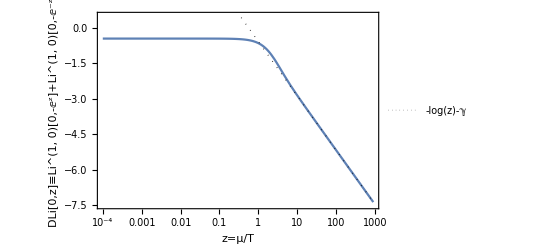

```mathematica
LogLinearPlot[Actor`DLiRePolyGamma[0,z],{z,10^-4,900},Frame->True,PlotRange->{All,{-7.5,0.5}},GridLines->{None,{{0,Directive[Black]},{Log[2/π],Directive[Black,Dashed]}}},GridLinesStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"z=μ/T","DLi[0,z]≡Li^(1, 0)[0,-ⅇ^z]+Li^(1, 0)[0,-ⅇ^-z]"},FrameTicks->{{Automatic,{Log[2/π]}},{Automatic,Automatic}}];
LogLinearPlot[-EulerGamma-Log[z],{z,10^-4,900},PlotStyle->Directive[Black,Thickness[0.002],Dotted],PlotLegends->Placed[{-EulerGamma-Log[z]},{Left,Bottom}]];
Show[{%%,%}]
```

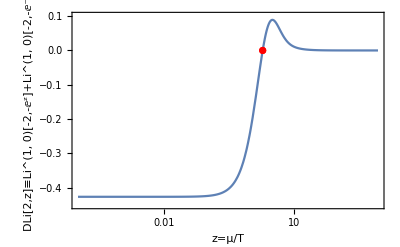

```mathematica
Show[{LogLinearPlot[Actor`DLiRePolyGamma[2,z],{z,10^-4,900},Frame->True,PlotRange->{All,{-0.45,0.1}},GridLines->{{{Actor`DLi2`roots[[1]],Directive[Black,Dashed]}},{{0,Directive[Black]},{-(7 Zeta[3])/(2 π^2),Directive[Black,Dashed]}}},GridLinesStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"z=μ/T","DLi[2,z]≡Li^(1, 0)[-2,-ⅇ^z]+Li^(1, 0)[-2,-ⅇ^-z]"},FrameTicks->{{Automatic,{0,-(7 Zeta[3])/(2 π^2)}},{Automatic,N[Actor`DLi2`roots,2]}}],ListLogLinearPlot[{Actor`DLi2`roots,0*Actor`DLi2`roots}ᵀ,PlotStyle->Red]}]
```

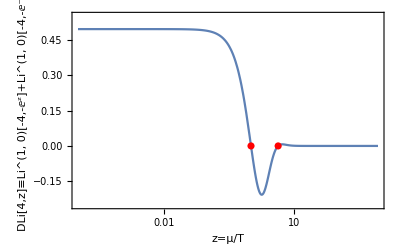

```mathematica
Show[{LogLinearPlot[Actor`DLiRePolyGamma[4,z],{z,10^-4,900},Frame->True,PlotRange->{All,{-0.25,0.55}},GridLines->{({#,Directive[Black,Dashed]}&/@Actor`DLi4`roots),{{0,Directive[Black]},{(93 Zeta[5])/(2 π^4),Directive[Black,Dashed]}}},FrameLabel->{"z=μ/T","DLi[4,z]≡Li^(1, 0)[-4,-ⅇ^z]+Li^(1, 0)[-4,-ⅇ^-z]"},GridLinesStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{Automatic,{(93 Zeta[5])/(2 π^4),0}},{Automatic,N[Actor`DLi4`roots,2]}}],ListLogLinearPlot[{Actor`DLi4`roots,0*Actor`DLi4`roots}ᵀ,PlotStyle->Red]}]
```

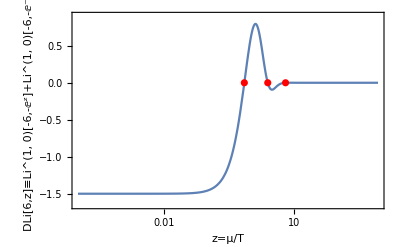

```mathematica
Show[{LogLinearPlot[Actor`DLiRePolyGamma[6,z],{z,10^-4,900},Frame->True,PlotRange->{All,{-1.65,0.9}},GridLines->{({#,Directive[Black,Dashed]}&/@Actor`DLi6`roots),{{0,Directive[Black]},{-(5715 Zeta[7])/(4 π^6),Directive[Black,Dashed]}}},FrameLabel->{"z=μ/T","DLi[6,z]≡Li^(1, 0)[-6,-ⅇ^z]+Li^(1, 0)[-6,-ⅇ^-z]"},GridLinesStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{Automatic,{-(5715 Zeta[7])/(4 π^6),0}},{Automatic,N[Actor`DLi6`roots,2]}}],ListLogLinearPlot[{Actor`DLi6`roots,0*Actor`DLi6`roots}ᵀ,PlotStyle->Red]}]
```

## Zero temperature Limit: Ω_F(∞,M,μ,a=0) using density of states

lim_(β→∞) Ω_F[β,β Δ,β μ]/V=- d/2 a_s/(2π)^s∫_0^∞ ⅆk k^(s-1)(μ-ω)θ[μ-ω]≡-∫_0^∞ ⅆE ρ_s[E](μ-E)θ[μ-E], with the Density of states ρ_s[E]≡ d/(2^s π^(s/2)Gamma[s/2])E(E^2-M^2)^(-1+s/2)θ[E-M]

Actor`ρs[s_,e_]:= d/(2^s π^(s/2)Gamma[s/2])e(e^2-M^2)^(-1+s/2)*HeavisideTheta[e-M];
ClearAll[Actor`ΩfzeroT];
Actor`ΩfzeroT[s_]:=Integrate[
	-Actor`ρs[s,e](μ-e)*HeavisideTheta[μ-e],
{e,0,∞},Assumptions→{M>0,μ>0,M<=μ}]+Integrate[
	-Actor`ρs[s,e](μ-e)*HeavisideTheta[μ-e],
{e,0,∞},Assumptions→{M>0,μ>0,M>μ}]HeavisideTheta[M-μ]

Actor`ΩfzeroT[1]:=(d*(-(μ*Sqrt[-Δ^2 + μ^2]) + Δ^2*ArcSinh[Sqrt[-1 + μ^2/Δ^2]])*HeavisideTheta[-Δ + μ])/(4*Pi)
Actor`ΩfzeroT[3]:=(d*(μ*(5*Δ^2 - 2*μ^2)*Sqrt[-Δ^2 + μ^2] - 3*Δ^4*ArcSinh[Sqrt[-1 + μ^2/Δ^2]])*HeavisideTheta[-Δ + μ])/(96*Pi^2)

ΩfzeroT[1]/.ArcSinhRules[μ,M]/.M→Δ
%-(d (-μ √(-Δ^2+μ^2)+Δ^2 ArcSinh[√(-1+μ^2/Δ^2)]) HeavisideTheta[-Δ+μ])/(4 π)//TrigToExp//Simplify[#,Assumptions→{Δ>0,μ>0,Δ<μ}]&

ΩfzeroT[3]/.ArcSinhRules[μ,M]/.M→Δ
%-(d HeavisideTheta[-Δ+μ] (μ (5 Δ^2-2 μ^2) √(-Δ^2+μ^2)+3 Δ^4 Log[Δ/(μ+√(-Δ^2+μ^2))]))/(96 π^2)//TrigToExp//Simplify[#,Assumptions→{Δ>0,μ>0,Δ<μ}]&

### Asymptotic expansion of ArcSin[√(μ^2/Δ^2-1)] around Δ→0 ⇔√(μ^2/Δ^2-1)→∞

Actor`ArcSinhAsymptz[z_,nmax_]:=Log[2z]+Sum[(-1)^(n-1)((2n-1)!!)/(2n (2n)!!)1/z^(2n),{n,1,nmax}]
Actor`ArcSinhAsymptΔ[nmax_/;(IntegerQ[nmax]&&nmax>=0)]:=Log[2μ]-Log[Δ]-Sum[(2^(-1-n) (-1+2 n)!!)/(n^2 (-1+n)!)Δ^(2n)/μ^(2n),{n,1,nmax}]
Actor`ArcSinhAsymptΔ[nmax_]:=Log[2μ]-Log[Δ]-Inactive[Sum][(2^(-1-n) (-1+2 n)!!)/(n^2 (-1+n)!)Δ^(2n)/μ^(2n),{n,1,nmax}]

Actor`ArcSinhRules[μ_:μ,Δ_:Δ]:={ArcCoth[μ/(√(μ^2-Δ^2))]->ArcSinh[√(μ^2/Δ^2-1)],Log[(μ+√(μ^2-Δ^2))/Δ]->ArcSinh[√(μ^2/Δ^2-1)],Log[Δ/(μ+√(μ^2-Δ^2))]→-ArcSinh[√(μ^2/Δ^2-1)]}

ArcSinh[z]=Log[2 z]+1/(4 z^2)-3/(32 z^4)+5/(96 z^6)-35/(1024 z^8)+... =Log[2z]+∑_(n=1)^∞ (-1)^(n-1)((2n-1)!!)/(2n (2n)!!)1/z^(2n); [AS70,4.6.31]
ArcSinh[√(μ^2/Δ^2-1)]=Log[2μ]-Log[Δ]-Δ^2/(4 μ^2)-(3 Δ^4)/(32 μ^4)-(5 Δ^6)/(96 μ^6)=Log[2μ]-Log[Δ]-∑_(n=1)^∞ (2^(-1-n) (-1+2 n)!!)/(n^2 (-1+n)!)Δ^(2n)/μ^(2n)

ArcSinhAsymptΔ[12]
%-Log[2 √(μ^2/Δ^2)]//Normal;
CoefficientList[%/.μ->1,Δ]//DeleteDuplicates
%[[2;;]]//FindSequenceFunction[#,n]&
%//FunctionExpand
%/.Gamma[n_+1/2]:>((2n-1)!!)/2^n Gamma[1/2](*[https://dlmf.nist.gov/5.4] or [AS70,6.1.12]*)/.Gamma[n_]:>(n-1)!

ArcSinhAsymptz[z,12]
Series[ArcSinhAsymptz[√(μ^2/Δ^2-1),12],{Δ,0,2*12}]//PowerExpand//Simplify
ArcSinhAsymptΔ[12]

Simplify[ArcCoth[μ/(√(μ^2-Δ^2))]-ArcSinh[√(μ^2/Δ^2-1)]//TrigToExp,Assumptions→{Δ<μ,μ>0,Δ>0}];
FullSimplify[ Log[(μ+√(μ^2-Δ^2))/Δ]-ArcSinh[√(μ^2/Δ^2-1)]//TrigToExp,Assumptions→{μ>0,Δ>μ,Δ>0}];

## (Generalized) Ginzburg-Landau expansion

[H. Abuki, D. Ishibashi and K. Suzuki - 2011 - Crystalline chiral condensates off the tricritical point in a generalized GL approach] [AIS1]
Note that we use different conventions for the factors of the GL coefficients α2_AIS=2α2, α4_AIS=4α4, and α6_AIS=6α6 ⇒ α2=(4 α4^2)/(3 α6)η2_AIS, cf.[AIS] Eq. (1) with the following expressions in this chapter. 

[A. Ahmed - 2018 - Ginzburg-Landau Type Approach to the 1+1 Gross Neveu Model - Beyond Lowest Non-Trivial Order]

## Derivations and Formulae

ToExpression["α"<>ToString[2(#-1)]]Δ^(2(#-1))&/@Range[3]//Total
Solve[D[%,Δ]==0,Δ]
D[%%,{Δ,2}]/.%
Plot[%%%/.{α0→0,α2→0,α4→1},{Δ,0,1}]

V_GL^2=α0+α2 Δ^2+α4 Δ^4;α4>0
α2>0: Δ=0: global minimum
α2<0: Δ=0: local maximum, Δ^2=-α2/(2 α4): global minium
α2=0_-: second order PT (α2==0): global minium Δ^2=-α2/(2 α4) merges into local maximum at Δ=0, becoming the global minimum at and beyond α=0

α4^2-3 α2 α6/.α2->η2 α4^2/α6;
%/α4^2//Expand
-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6)/.α2->η2 α4^2/α6//Simplify
%/.η2->1/4//Simplify
Simplify[%/.α4->-α4Abs,Assumptions→α4Abs>0]

ToExpression["α"<>ToString[2(#-1)]]Δ^(2(#-1))&/@Range[4]//Total
Solve[D[%,Δ]==0,Δ]//Simplify//DeleteDuplicates
Δ^2/.%//DeleteDuplicates//Expand
(%%%/.Δ→√(%[[3]]))-%%%/.Δ→0//Simplify
Solve[0==%,α2]

V_GL^3[Δ^2]=α0+α2 Δ^2+α4 Δ^4+α6 Δ^6;α6>0
α2->η2 α4^2/α6
α2<0: Δ=0 local Maximum, global minimum at Δ^2=-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6) which aproaches Δ=0 for α2→0_- again second order PT for  α2→0_- independent of α_4 in this case;
α2>0,α4^2-3 α2 α6<0: local Minimum at Δ=0, restored phase;
α2>0,α4<0,α4^2-3 α2 α6>0;
	 local Minima at Δ=0, Δ^2=-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6), 
	local maximum at Δ^2=-α4/(3 α6)-(√(α4^2-3 α2 α6))/(3 α6): Spinodal region
	V_GL^3[Δ=0]==V_GL^3[Δ=-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6)]⇒ α6 α2-α4^2/4==0, first order phase transition ( α6 α2-α4^2/4==0⇔α2==1/4 α4^2/α6⇔η2=1/4)(GL), [AIS1] η2_AIS=1/4 (α2=(4 α4^2)/(3 α6)η2_AIS)

	α2→0_+: local maximum at Δ^2=-α4/(3 α6)-(√(α4^2-3 α2 α6))/(3 α6) vanishes into Δ=0, Δ=0 changes from a local minimum so a local maximum, left spinodal line at (α2==0)(GL==physical)
	α4^2-3 α2 α6→0_+: local maximum at Δ^2=-α4/(3 α6)-(√(α4^2-3 α2 α6))/(3 α6)  approaches local minimum at Δ^2=-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6) which becomes a maximum, right spinodal line  (α4^2-3 α2 α6==0⇔α2==1/3 α4^2/α6⇔η2=1/3) (GL)
	α4→0_-: aproaching CP: all extrema merge into Δ=0

## Implementation

ClearAll[GL`lines`compute];
GL`lines`compute[αi_,range_,gGLQ_:False,opts_:{}]:=Module[{α2,α4,α6,ti,μi,plot,CP,TC,asoc,
	α2plot,α2plotC,α2lines,α4plot,α4plotC,α4lines,α6plot,α6plotC,α6lines,
	rSLplot,rSLplotC,rSLlines,rSLα4lines,rSLlinesRaw,foPBplot,foPBplotC,foPBlines,foPBα4lines,foPBlinesRaw,
	gGLη2HBPplotC,gGLη2HBPlines,gGLη2HBPFalseLines,gGLη2HBPplot,
	gGLη2SPplotC,gGLη2SPlines,gGLη2SPFalseLines,gGLη2SPplot
	},
	{α2,α4,α6}=αi[[2;;4]];
	
	α2plotC=ContourPlot[α2[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α2lines=Cases[Normal@α2plotC,Line[pts__]:>pts,Infinity];
	α2plot=ListLinePlot[α2lines,PlotStyle→Red];
	
	α4plotC=ContourPlot[α4[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α4lines=Cases[Normal@α4plotC,Line[pts__]:>pts,Infinity];
	α4plot=ListLinePlot[α4lines,PlotStyle→Blue];
	
	α6plotC=ContourPlot[α6[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α6lines=Cases[Normal@α6plotC,Line[pts__]:>pts,Infinity];
	α6plot=ListLinePlot[α6lines,PlotStyle→Purple];
	
	rSLplotC=ContourPlot[α4[μ,T]^2-3 α2[μ,T]*α6[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	rSLlinesRaw=Cases[Normal@rSLplotC,Line[pts__]:>pts,Infinity];
	rSLlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,rSLlinesRaw]/.{}→Nothing;
	rSLlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],rSLlines]/.{}→Nothing;
	rSLα4lines=If[α4[#[[1,1]],#[[1,2]]]>=0,#,Nothing]&/@Flatten[rSLlines,1];
	rSLlines=Complement[Flatten[rSLlines,1],rSLα4lines];
	rSLplot=Show[{ListLinePlot[rSLlines,PlotStyle→Magenta],ListLinePlot[rSLα4lines,PlotStyle→{{Magenta,Dashed}}]}];
	
	foPBplotC=ContourPlot[α6[μ,T]*α2[μ,T]-α4[μ,T]^2/4,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	foPBlinesRaw=Cases[Normal@foPBplotC,Line[pts__]:>pts,Infinity];
	foPBlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,foPBlinesRaw]/.{}→Nothing;
	foPBlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],foPBlines]/.{}→Nothing;
	foPBα4lines=If[α4[#[[1,1]],#[[1,2]]]>=0,#,Nothing]&/@Flatten[foPBlines,1];
	foPBlines=Complement[Flatten[foPBlines,1],foPBα4lines];
	foPBplot=Show[{ListLinePlot[foPBlines,PlotStyle→Green],ListLinePlot[foPBα4lines,PlotStyle→{{Green,Dashed}}]}];
			
	TC=Missing[];
	If[Length[α2lines]===1,
		TC=Last@First@Sort[α2lines[[1]],#1[[1]]<#2[[1]]&]
	];
		
	CP=Missing[];
	If[Length[α2lines]===1&&Length[α4lines]===1,
		CP=First@Sort[Flatten[Map[p1↦Map[p2↦{p1,p2,Norm[p1-p2]},α4lines[[1]]],α2lines[[1]]],1],#1[[3]]<#2[[3]]&];
		Module[{α2p1,α2p2,α4p1,α4p2,x,y},
			α2p1=Nearest[α2lines[[1]],CP[[1]],2];
			If[Length[α2p1]<2,Goto["end"],α2p2=α2p1[[2]];α2p1=α2p1[[1]];];
			
			α4p1=Nearest[α4lines[[1]],CP[[2]],2];
			If[Length[α4p1]<2,Goto["end"],α4p2=α4p1[[2]];α4p1=α4p1[[1]];];
			
			CP=α2p1+(α2p2-α2p1)x/.First@Solve[{α2p1+(α2p2-α2p1)x==α4p1+(α4p2-α4p1)y},{x,y}];
			
			Label["end"]
		];
	];
	
	plot=Show[{α2plot,α4plot,α6plot,rSLplot,foPBplot,If[MissingQ[CP],Nothing,ListPlot[{CP},PlotStyle→Red]]},Frame→True,PlotRange→range,GridLines->Automatic];
	asoc={
		"plot"->plot,"α2=0"->α2lines,"α4=0"->α4lines,"α6=0"->α6lines,"αrSL"->rSLlines,"αrSLα4"->rSLα4lines,"α1stOPB"->foPBlines,"α1stOPBα4"->foPBα4lines,"CP"→CP,"TC"→TC,
		"plotC"->{α2plotC,α4plotC,α6plotC,rSLplotC,foPBplotC},"rSLlinesRaw"->rSLlinesRaw,"foPBlinesRaw"->foPBlinesRaw
	};
	
	If[gGLQ=!=False,
		(*else: generalized GL [AIS]]*)
		Block[{η2HBP,η2SP},
		{η2HBP,η2SP}=If[ListQ[gGLQ],gGLQ[[1;;2]],{0.2289231935942564819063807109,1/2}(*CDW values*)];
		
			gGLη2HBPplotC=ContourPlot[α6[μ,T]*α2[μ,T]-η2HBP*α4[μ,T]^2,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
			gGLη2HBPlines=Cases[Normal@gGLη2HBPplotC,Line[pts__]:>pts,Infinity];
			gGLη2HBPlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,gGLη2HBPlines]/.{}→Nothing;
			gGLη2HBPlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],gGLη2HBPlines]/.{}→Nothing;
			gGLη2HBPFalseLines=If[α4[#[[1,1]],#[[1,2]]]>0,#,Nothing]&/@Flatten[gGLη2HBPlines,1];
			gGLη2HBPlines=Complement[Flatten[gGLη2HBPlines,1],gGLη2HBPFalseLines];
			gGLη2HBPplot=Show[{ListLinePlot[gGLη2HBPlines,PlotStyle→Orange],ListLinePlot[gGLη2HBPFalseLines,PlotStyle→{{Orange,Dashed}}]}];
			
			gGLη2SPplotC=ContourPlot[α6[μ,T]*α2[μ,T]-η2SP*α4[μ,T]^2,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
			gGLη2SPlines=Cases[Normal@gGLη2SPplotC,Line[pts__]:>pts,Infinity];
			gGLη2SPlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,gGLη2SPlines]/.{}→Nothing;
			gGLη2SPlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],gGLη2SPlines]/.{}→Nothing;
			gGLη2SPFalseLines=If[α4[#[[1,1]],#[[1,2]]]>0,#,Nothing]&/@Flatten[gGLη2SPlines,1];
			gGLη2SPlines=Complement[Flatten[gGLη2SPlines,1],gGLη2SPFalseLines];
			gGLη2SPplot=Show[{ListLinePlot[gGLη2SPlines,PlotStyle→Darker@Orange],ListLinePlot[gGLη2SPFalseLines,PlotStyle→{{Darker@Orange,Dashed}}]}];
			
			plot=Show[{plot,gGLη2HBPplot,gGLη2SPplot}];
			asoc=Join[asoc,{
				"gGLη2HBPplotC"->gGLη2HBPplotC,"gGLη2HBPlines"->gGLη2HBPlines,"gGLη2HBPFalseLines"->gGLη2HBPFalseLines,"gGLη2HBPplot"->gGLη2HBPplot,
				"gGLη2SPplotC"->gGLη2SPplotC,"gGLη2SPlines"->gGLη2SPlines,"gGLη2SPFalseLines"->gGLη2SPFalseLines,"gGLη2SPplot"->gGLη2SPplot
			}]/.Rule["plot",_]:>Rule["plot",plot];
		];		
	];
	
	GL`lines[Association[asoc]]
]/;ListQ[αi]&&Length[αi]==4

ClearAll[GL`lines];
(** Getter **)
GL`lines[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
GL`lines[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(** StandardForm **)
MakeBoxes[GL`lines[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{plot},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	plot=With[{a=asoc["plot"]},If[MissingQ[a],None,Show[{a},ImageSize→150]]];
	BoxForm`ArrangeSummaryBox[GL`lines,
		GL`lines[asoc],
		plot,
		{""},
		{},
		StandardForm,
		"Interpretable"→True
	]
]

GL`potential`Δmin[μi_,Ti_,αiFkts_]:=Module[{αi,terms,U,dU,ddU,Δ,Δroots,ΔrootsTable},
	αi=#[μi,Ti]&/@αiFkts;
	terms=Length[αi]-1;
	
	U=Inactive[Function][{Δ},αi.Array[Δ^(2(#-1))&,terms+1]]//Activate;
	dU=Inactive[Function][{Δ},D[U[Δ],Δ]]//Activate;
	ddU=Inactive[Function][{Δ},D[dU[Δ],Δ]]//Activate;
	
	Δroots=Solve[0==dU[Δ],Δ]/.{{Rule[Δ,x_]}:>Nothing/;(Abs[Im[x]]>0||Re[x]<0)}//Flatten//Part[#,All,2]&//Sort;
	ΔrootsTable=SortBy[{#,U[#],ddU[#]}&/@Δroots,#[[2]]&]
]

ClearAll[GL`potential`compute];
GL`potential`compute[μi_,Ti_,αiFkts_,plotOptions_:{},plotRange_:Automatic,fullFkt_:None,fullFktOpts_:{},plotQ_:True]:=Module[{αi,terms,U,dU,ddU,Δ,Δroots,ΔrootsTable,Δimin,plot,Δmax,αsignFkt,fullPlot,fullPlotData,fullMin},
	αi=#[μi,Ti]&/@αiFkts;
	terms=Length[αi]-1;
	
	U=Inactive[Function][{Δ},αi.Array[Δ^(2(#-1))&,terms+1]]//Activate;
	dU=Inactive[Function][{Δ},D[U[Δ],Δ]]//Activate;
	ddU=Inactive[Function][{Δ},D[dU[Δ],Δ]]//Activate;
	
	Δroots=Solve[0==dU[Δ],Δ]/.{{Rule[Δ,x_]}:>Nothing/;(Abs[Im[x]]>0||Re[x]<0)}//Flatten//Part[#,All,2]&//Sort;
	ΔrootsTable={#,U[#],ddU[#]}&/@Δroots;
	Δmax=Max[Δroots,If[NumberQ@plotRange,plotRange,0]];
	Δimin=Select[ΔrootsTable,#[[3]]>0&];
	Δimin=If[Length[Δimin]===0,Missing[],TakeSmallestBy[Δimin,#[[2]]&,1]//First//First];
	If[Δmax==0.,Δmax=1;];
	
	If[fullFkt=!=None,
		fullPlotData=Table[With[{x=i/100*Δmax},{x,fullFkt[μi,Ti][x][fullFktOpts]}],{i,0,200}];
		fullMin=First[SortBy[fullPlotData,Last]];
		fullPlot=Show[{ListLinePlot[fullPlotData,PlotStyle→Gray],ListPlot[{fullMin},PlotStyle→Gray,PlotMarkers→"OpenMarkers"]}];
		Δmax=Max[fullMin[[1]],Δmax];
		,(*else*)
		fullPlot=Nothing;
	];
	If[plotQ===True,
		plot=Show[{
			Plot[U[Δ],{Δ,-1.1*Δmax,1.1*Δmax},
				PlotLabel→Row[{Row[{"μ=",N@Round[μi,10^-3]}],Row[{"T=",N@Round[Ti,10^-3]}]}~Join~MapThread[Row[{Subscript["α",2#1],"=",ScientificForm[N@#2,2]}]&,{(Range[terms]),αi[[2;;]]}],","],
				Frame→True,PlotRange→{{0,Δmax},Full},PlotRangePadding→Scaled[.05],GridLines→Automatic,Axes→True,##
			]&@@plotOptions,
			ListPlot[ΔrootsTable[[All,{1,2}]]],
			fullPlot
		},PlotRange→{{0,Δmax},Full}];,(*else*)
		plot=Graphics[];
	];
	
	GL`potential[<|"plot"→plot,"Δroots"->Δroots,"ΔrootsTable"->ΔrootsTable,"Δimin"->Δimin,"U"→U,"αi"->αi,"μ"→μi,"T"→Ti,"Δmax"->Δmax|>]
]/;ListQ[αiFkts]&&(1≤Length[αiFkts]≤4)

ClearAll[GL`potential]
(** Getter **)
GL`potential[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
GL`potential[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]
GL`potential[asoc_][]:=asoc["plot"]
GL`potential[asoc_][x_/;NumberQ[x]]:=asoc["U"][x]

(** StandardForm **)
MakeBoxes[GL`potential[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{plot},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	plot=With[{a=asoc["plot"]},If[MissingQ[a],None,Show[{a},ImageSize→200]]];
	BoxForm`ArrangeSummaryBox[GL`potential,
		GL`potential[asoc],
		plot,
		{""},
		{},
		StandardForm,
		"Interpretable"→True
	]
]